```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject(1,local),KernelObject(2,local)}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[2,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[40/25 10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[0,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
(*χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 0.

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=40;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
(*n=1.49669+0.00785λ^(−2)+0.00026λ^(−4)(*обыкновенная*)
n=1.4990+0.0072λ^(−2)+0.0003λ^(−4)*)
(*n=1.67798+0.01696λ^(−2)+0.00127λ^(−4)(*необыкновенная*)
n=1.6933+0.0078λ^(−2)+0.0028λ^(−4)*)
ϵpp[k0_]=SetPrecision[2.22,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[2.49,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика q: ",qc mee, " эВ"]
Print["Толщина пластины холестерика Lz: ",Lz lc 10^4, " мкм"]
(*Print["Плазменная частота: ",ωp mee," эВ,  ",2.42 10^(14) ωp mee," Гц"]*)
Module[{xx=5/mee},(*предполагаемая энергия фотона*)
Print["Анизотропия de: ",dec[xx]];
Print["Параметр ВКБ: ", (dec[xx] ϵpp[xx]^(1/2) xx/(4 qc))^2]]
```

Волновой вектор холестерика q: 0.774583 эВ

Толщина пластины холестерика Lz: 32. мкм

Анизотропия de: 0.121622

Параметр ВКБ: 0.0855182

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=(√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1+(kp^2 (-(4 (√(k0s (de (de k0s+8)+16))+4))-de (de k0s+√(k0s (de (de k0s+8)+16))+4)))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√((de k0s)/2-1/2 √(k0s (de (de k0s+8)+16))+k0s+1)+1+(-de (-de k0s+√(k0s (de (de k0s+8)+16))-4)-4 √(k0s (de (de k0s+8)+16))+16)/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))) kp^2;(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;
xmsm2=-(2 (-((√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1)^2+(de k0s)/2+k0s))/(de k0s)+kp^2 ((√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4)/(2 de k0s^2)-(2 (((4 (√(k0s (de (de k0s+8)+16))+4)+de (de k0s+√(k0s (de (de k0s+8)+16))+4)) (√2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+2))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)))-de/4-1))/(de k0s));
xps2=-kp^2 ((de (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xms0=-kp^2 (((de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4) (√(k0s (de (de k0s+8)+16))+6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xpsm2=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20) (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xmsm4=-kp^2 ((de(de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));

(*медленная волна*)
yps0=1;
ymsm2=-(2 (-1/4 (√(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+2)^2+(de k0s)/2+k0s))/(de k0s)+(kp^2 (k0s (-(√2 de^2 k0s)+√2 de √(k0s (de (de k0s+8)+16))-4 de √((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)-4 √2 (3 de+4))+4 (√2 √(k0s (de (de k0s+8)+16))+√(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)))))/(2 de k0s^2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)));
yps2=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));
yms0=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20) (-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ypsm2=-kp^2 (((-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4) (√(k0s (de (de k0s+8)+16))+6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ymsm4=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));

xmsm2=If[xmsm2∈Reals,xmsm2,0];(*коэффициенты должны быть вещественными*)
xps2=If[xps2∈Reals,xps2,0];
xms0=If[xms0∈Reals,xms0,0];
xpsm2=If[xpsm2∈Reals,xpsm2,0];
xmsm4=If[xmsm4∈Reals,xmsm4,0];
ymsm2=If[ymsm2∈Reals,ymsm2,0];(*коэффициенты должны быть вещественными*)
yps2=If[yps2∈Reals,yps2,0];
yms0=If[yms0∈Reals,yms0,0];
ypsm2=If[ypsm2∈Reals,ypsm2,0];
ymsm4=If[ymsm4∈Reals,ymsm4,0];

xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=1/rff^2;(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
apss=ts(yps0+yps2 r+ypsm2/r);
amss=ts (yms0+ymsm2/r+ymsm4/r^2);
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
amscs=1/ts (yps0 +yps2/r+ypsm2 r);
apscs=1/ts(yms0+ymsm2 r+ymsm4 r^2);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2)/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2)/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4)/r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2)/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2)/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4)/r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2)/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf ((pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2) r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4) r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4))));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2)/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2) r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4) r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al,{xmsm2,xps2,xms0,xpsm2,xmsm4},{ymsm2,yps2,yms0,ypsm2,ymsm4}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,xmsm2_?NumberQ,xps2_?NumberQ,xms0_?NumberQ,xpsm2_?NumberQ,xmsm4_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,xms2,xpsm4,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
xms2=0;xpsm4=0;(*зануляем высшие поправки*)

tf=Exp[I pf tetb];r=rf1;(*фазовые множители*)

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+(pf+2) xps2 r+(pf-2) xpsm2/r)+(pf xms0+(pf-2) xmsm2/r+(pf-4) xmsm4/r^2));
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+(pf+2) xps2/r+(pf-2) xpsm2 r)+(pf xms0+(pf-2) xmsm2 r+(pf-4) r^2xmsm4));

{{apfs rff,amfs/rff,a3fs},{apfcs rff,amfcs/rff,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,ymsm2_?NumberQ,yps2_?NumberQ,yms0_?NumberQ,ypsm2_?NumberQ,ymsm4_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,yms2,ypsm4,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
yms2=0;ypsm4=0;(*зануляем высшие поправки*)

ts=Exp[I ps tetb];r=rf1;(*фазовые множители*)

apss=ts (yps0+yps2 r+ypsm2/r);(*a_pm,3*)
amss=ts(yms0+ymsm2/r+ymsm4/r^2);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+(ps+2) yps2 r+(ps-2) ypsm2/r)+(ps yms0+(ps-2) ymsm2/r+(ps-4) ymsm4/r^2));
amscs=1/ts (yps0+yps2/r+ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts (yms0+ymsm2 r+r^2ymsm4);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+(ps+2) yps2/r+(ps-2) ypsm2 r)+(ps yms0+(ps-2) ymsm2 r+(ps-4) r^2ymsm4));

{{apss rff,amss/rff,a3ss},{apscs rff,amscs/rff,a3scs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,achli_,xxsl_,yysl_,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t,tet},
tet=qc x3[t]-ϕ;
rfff=Exp[2 I tet];(*фазовый множитель*)

afrl=ModeFun1[tet,kp,rff,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],pf,k3b,rfff];
asrl=ModeFun2[tet,kp,rff,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
Clear[AmplitPlane]
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*,MaxRecursion->12,MinRecursion->5*)(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*,MaxRecursion->12,MinRecursion->5*)(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2];(*вероятность в единицу телесного угла на единичный интервал энергии*)

dProbabPlane0[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*,MaxRecursion->12,MinRecursion->5*)(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=0;(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
(*-------примеры-------*)
```

```mathematica
(*спектр*)
```

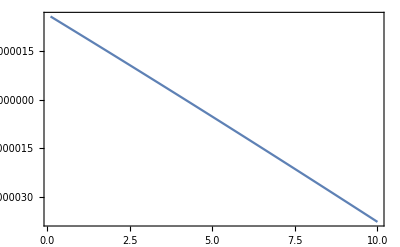
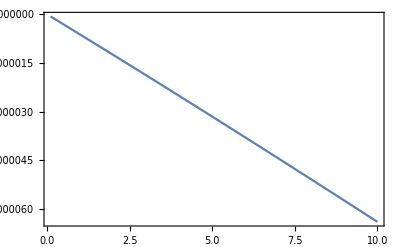
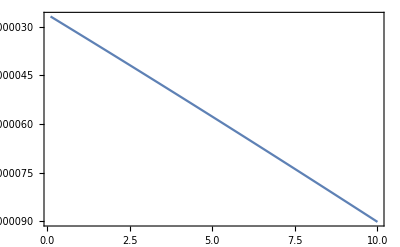
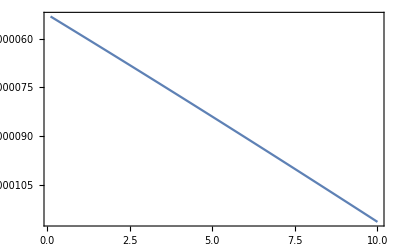

```mathematica
{Plot[EqnSpecX[xx/mee,1/5,-2],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,0],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,1],{xx,1/10,10},Frame->True,PlotRange->Full]}
```

```mathematica
EqnSpecX[xx/mee,1/5,-2]/.{xx->1/10}
EqnSpecX[xx/mee,1/5,-1]/.{xx->1/10}
EqnSpecX[xx/mee,1/5,0]/.{xx->1/10}
```

2.56336×10^-6

-6.21118×10^-8

-2.68759×10^-6

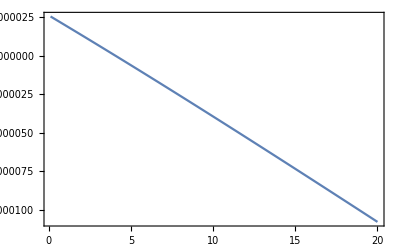
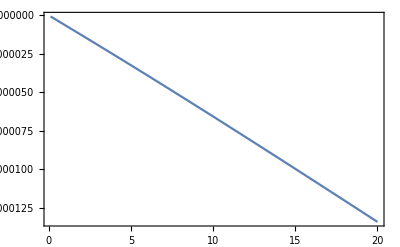
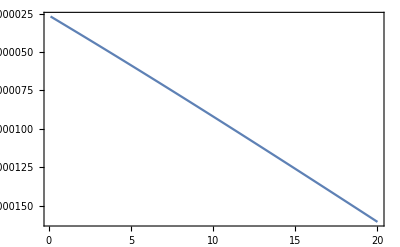
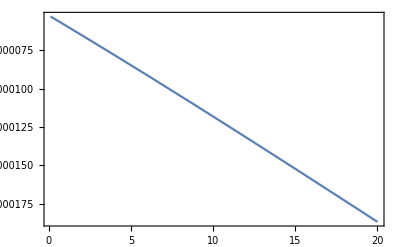

```mathematica
{Plot[EqnSpecX[xx/mee,1/10,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

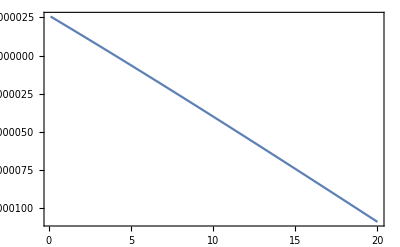
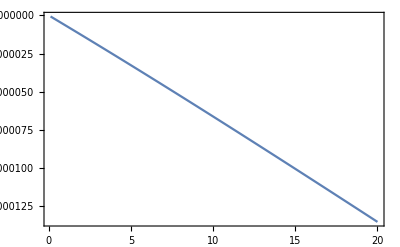
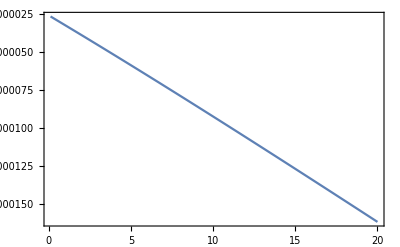
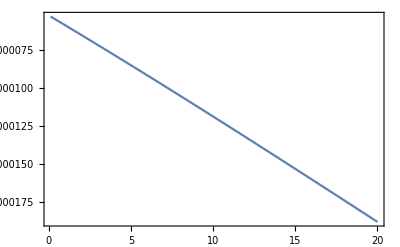

```mathematica
{Plot[EqnSpecX[xx/mee,1/100,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/100,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

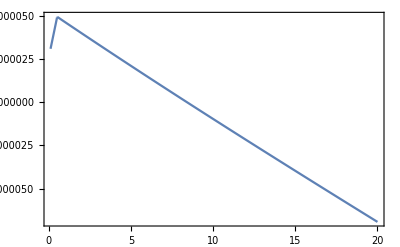
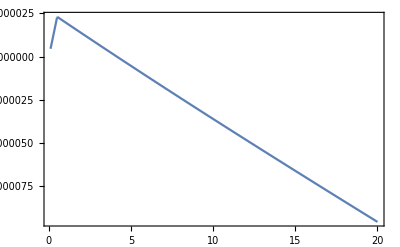
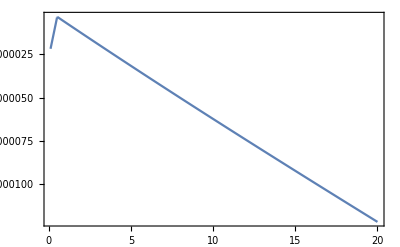
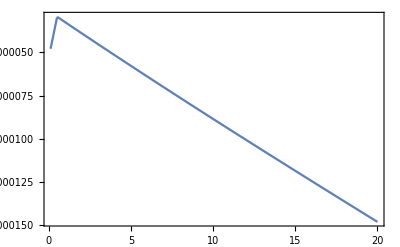

```mathematica
{Plot[EqnSpecY[xx/mee,1/100,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

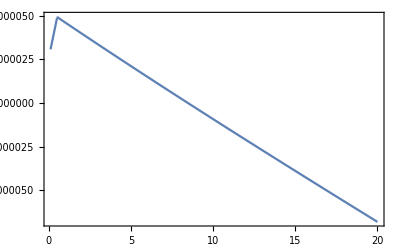
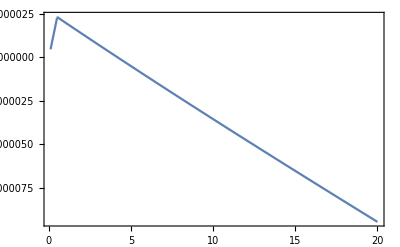
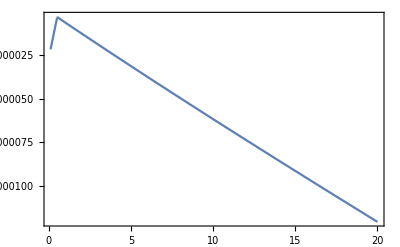
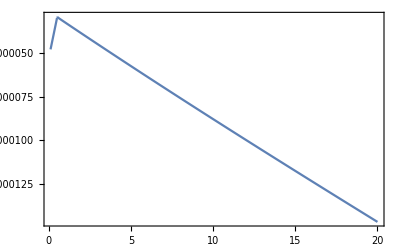

```mathematica
{Plot[EqnSpecY[xx/mee,1/10,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/100,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/100,-1],{xx,5}]
```

{xx→8.39094}

{xx→4.14168}

```mathematica
FindRoot[EqnSpecX[xx/mee,1/100,-2],{xx,5}]
```

{xx→4.03136}

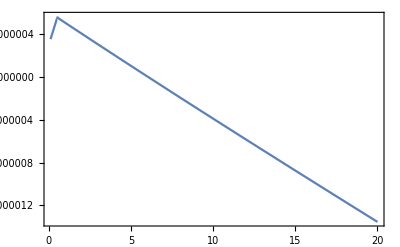
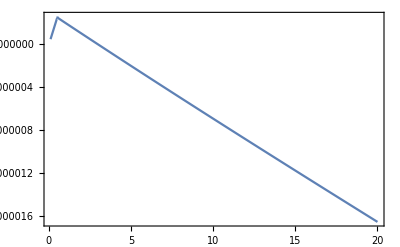
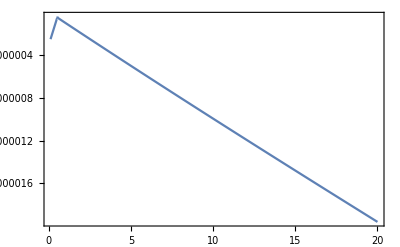
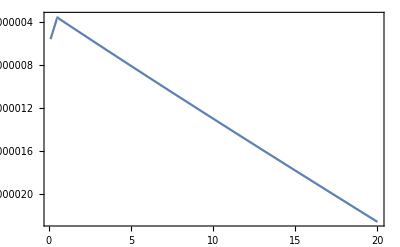

```mathematica
{Plot[EqnSpecY[xx/mee,1/5,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/5,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/5,-1],{xx,5}]
```

{xx→6.03793}

{xx→2.99827}

```mathematica
FindRoot[EqnSpecX[xx/mee,1/5,-2],{xx,5}]
```

{xx→2.95478}

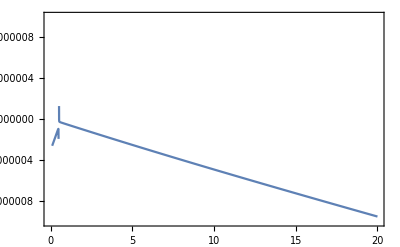

```mathematica
Plot[EqnSpecY[xx/mee,9/10,0],{xx,1/10,20},Frame->True,PlotRange->{-10^(-5),10^(-5)}]
```

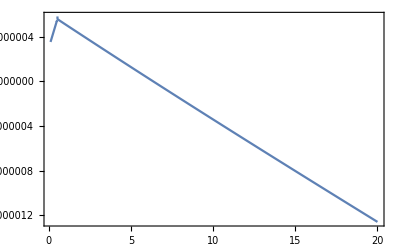
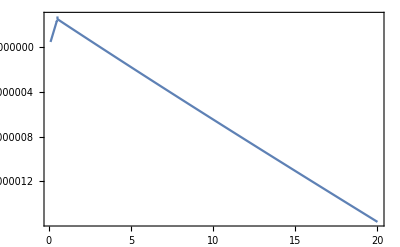
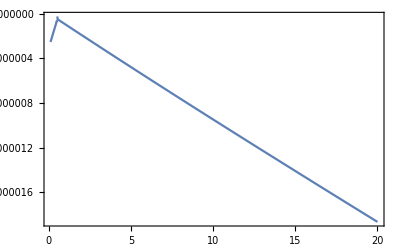
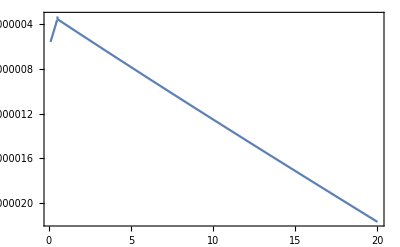

```mathematica
{Plot[EqnSpecY[xx/mee,1/3,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/3,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/3,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/3,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/2,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/2,-1],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/5,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/5,-1],{xx,5}]
```

{xx→7.01724}

{xx→3.47662}

{xx→6.03793}

{xx→2.99827}

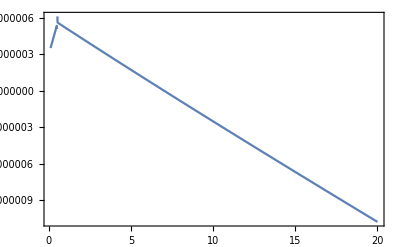
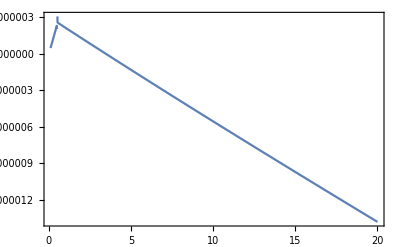
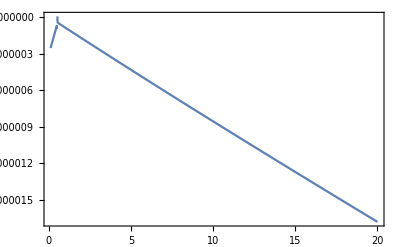
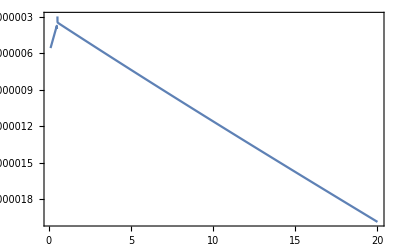

```mathematica
{Plot[EqnSpecY[xx/mee,1/2,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/2,-1],{xx,5}]
```

{xx→3.47662}

```mathematica
dProbabPlane[-1,4.14/mee,1/100,0]//Timing
dProbabPlane0[-1,4.14/mee,1/100,0]//Timing
dProbabPlane[1,4.14/mee,1/100,0]//Timing
dProbabPlane0[1,4.14/mee,1/100,0]//Timing
```

{3.97803,1.63091}

{4.02483,1.61094}

{5.53804,0.0934609}

{5.52244,0.0298339}

```mathematica
dProbabPlane[-1,4.14/mee,1/100,0]//Timing
dProbabPlane0[-1,4.14/mee,1/100,0]//Timing
dProbabPlane[1,4.14/mee,1/100,0]//Timing
dProbabPlane0[1,4.14/mee,1/100,0]//Timing
```

{4.13403,1.63091}

{4.14963,1.61094}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.72073×10^6}. NIntegrate obtained 4108.51+1783.92 ⅈ and 0.00765009 for the integral and error estimates.

{4.11843,0.0934609}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.72073×10^6}. NIntegrate obtained 4108.51+1783.92 ⅈ and 0.00765009 for the integral and error estimates.

{4.16523,0.0298339}

```mathematica
tk06s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/100,0]},{x,3,5,0.005}](*нужно еще посмотреть обыкновенную волну*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(3. | 0.323668
3.005 | 0.278127
3.01 | 0.187077
3.015 | 0.142739
3.02 | 0.0718315
3.025 | 0.0356201
3.03 | 0.00839413
3.035 | 0.00555016
3.04 | 0.0179782
3.045 | 0.0593606
3.05 | 0.100259
3.055 | 0.17247
3.06 | 0.227564
3.065 | 0.292515
3.07 | 0.359138
3.075 | 0.375479
3.08 | 0.436226
3.085 | 0.404573
3.09 | 0.410373
3.095 | 0.373776
3.1 | 0.308238
3.105 | 0.275848
3.11 | 0.183439
3.115 | 0.13901
3.12 | 0.0746982
3.125 | 0.0344628
3.13 | 0.0100471
3.135 | 0.00437524
3.14 | 0.015737
3.145 | 0.0530213
3.15 | 0.0943679
3.155 | 0.156817
3.16 | 0.218753
3.165 | 0.270956
3.17 | 0.345564
3.175 | 0.356833
3.18 | 0.41254
3.185 | 0.394159
3.19 | 0.385228
3.195 | 0.368548
3.2 | 0.293681
3.205 | 0.267536
3.21 | 0.180647
3.215 | 0.132128
3.22 | 0.0772518
3.225 | 0.0323901
3.23 | 0.0111831
3.235 | 0.00308399
3.24 | 0.0144236
3.245 | 0.0466749
3.25 | 0.0899413
3.255 | 0.142663
3.26 | 0.210119
3.265 | 0.253111
3.27 | 0.328635
3.275 | 0.341531
3.28 | 0.385725
3.285 | 0.384311
3.29 | 0.360806
3.295 | 0.358431
3.3 | 0.280542
3.305 | 0.253712
3.31 | 0.178282
3.315 | 0.123187
3.32 | 0.0782847
3.325 | 0.0298667
3.33 | 0.0113264
3.335 | 0.00191481
3.34 | 0.0137201
3.345 | 0.0410219
3.35 | 0.0865345
3.355 | 0.131228
3.36 | 0.200979
3.365 | 0.239143
3.37 | 0.308864
3.375 | 0.328941
3.38 | 0.358622
3.385 | 0.373322
3.39 | 0.338458
3.395 | 0.342349
3.4 | 0.26894
3.405 | 0.236063
3.41 | 0.175316
3.415 | 0.113239
3.42 | 0.0766659
3.425 | 0.0273058
3.43 | 0.0103498
3.435 | 0.0010558
3.44 | 0.0134841
3.445 | 0.0367392
3.45 | 0.0838555
3.455 | 0.123058
3.46 | 0.191052
3.465 | 0.228819
3.47 | 0.288001
3.475 | 0.318238
3.48 | 0.333568
3.485 | 0.359517
3.49 | 0.318862
3.495 | 0.321021
3.5 | 0.258537
3.505 | 0.216595
3.51 | 0.170276
3.515 | 0.10314
3.52 | 0.0719361
3.525 | 0.0249653
3.53 | 0.00847432
3.535 | 0.000562038
3.54 | 0.0137314
3.545 | 0.0342589
3.55 | 0.0817199
3.555 | 0.118196
3.56 | 0.180657
3.565 | 0.221739
3.57 | 0.268277
3.575 | 0.308384
3.58 | 0.311994
3.585 | 0.341962
3.59 | 0.302192
3.595 | 0.296573
3.6 | 0.24846
3.605 | 0.197014
3.61 | 0.161843
3.615 | 0.0934889
3.62 | 0.0645045
3.625 | 0.022842
3.63 | 0.0061281
3.635 | 0.000372149
3.64 | 0.0145542
3.645 | 0.0337353
3.65 | 0.0800193
3.655 | 0.116446
3.66 | 0.170716
3.665 | 0.217374
3.67 | 0.251527
3.675 | 0.298194
3.68 | 0.294502
3.685 | 0.321059
3.69 | 0.288141
3.695 | 0.271468
3.7 | 0.23736
3.705 | 0.178472
3.71 | 0.149588
3.715 | 0.0845621
3.72 | 0.0553445
3.725 | 0.0206422
3.73 | 0.00378713
3.735 | 0.000438873
3.74 | 0.0160203
3.745 | 0.035155
3.75 | 0.0787392
3.755 | 0.117493
3.76 | 0.16239
3.765 | 0.214919
3.77 | 0.238702
3.775 | 0.286569
3.78 | 0.280969
3.785 | 0.298328
3.79 | 0.275749
3.795 | 0.247531
3.8 | 0.223724
3.805 | 0.161473
3.81 | 0.134154
3.815 | 0.0762146
3.82 | 0.0455042
3.825 | 0.017921
3.83 | 0.0018573
3.835 | 0.000865859
3.84 | 0.0180939
3.845 | 0.0384339
3.85 | 0.0779828
3.855 | 0.120813
3.86 | 0.156467
3.865 | 0.212993
3.87 | 0.229651
3.875 | 0.272642
3.88 | 0.270275
3.885 | 0.275169
3.89 | 0.262905
3.895 | 0.225206
3.9 | 0.206145
3.905 | 0.145566
3.91 | 0.116519
3.915 | 0.0676539
3.92 | 0.0356764
3.925 | 0.0143327
3.93 | 0.000613014
3.935 | 0.00194629
3.94 | 0.02064
3.945 | 0.043382
3.95 | 0.0778006
3.955 | 0.125154
3.96 | 0.152467
3.965 | 0.208749
3.97 | 0.222148
3.975 | 0.254455
3.98 | 0.2584
3.985 | 0.250033
3.99 | 0.244215
3.995 | 0.201499
4. | 0.18152
4.005 | 0.127422
4.01 | 0.0957329
4.015 | 0.0562841
4.02 | 0.0254449
4.025 | 0.00951128
4.03 | 0.000291176
4.035 | 0.0042988
4.04 | 0.0237014
4.045 | 0.0493272
4.05 | 0.0768719
4.055 | 0.125547
4.06 | 0.14416
4.065 | 0.190545
4.07 | 0.201932
4.075 | 0.214845
4.08 | 0.220318
4.085 | 0.198172
4.09 | 0.18592
4.095 | 0.145115
4.1 | 0.116738
4.105 | 0.0740952
4.11 | 0.0458552
4.115 | 0.0183954
4.12 | 0.00621606
4.125 | 0.00412495
4.13 | 0.0235139
4.135 | 0.0454305
4.14 | 0.0934609
4.145 | 0.144548
4.15 | 0.188849
4.155 | 0.273024
4.16 | 0.293154
4.165 | 0.367492
4.17 | 0.38191
4.175 | 0.393282
4.18 | 0.415605
4.185 | 0.363924
4.19 | 0.361853
4.195 | 0.290301
4.2 | 0.245263
4.205 | 0.186925
4.21 | 0.121625
4.215 | 0.0812181
4.22 | 0.0314976
4.225 | 0.0117284
4.23 | 0.000012204
4.235 | 0.00756469
4.24 | 0.0281479
4.245 | 0.0708713
4.25 | 0.101616
4.255 | 0.169742
4.26 | 0.200304
4.265 | 0.251402
4.27 | 0.28921
4.275 | 0.292149
4.28 | 0.323572
4.285 | 0.28782
4.29 | 0.281199
4.295 | 0.236314
4.3 | 0.191264
4.305 | 0.150072
4.31 | 0.0935137
4.315 | 0.0606755
4.32 | 0.0217375
4.325 | 0.00659014
4.33 | 0.000590323
4.335 | 0.0124725
4.34 | 0.0323556
4.345 | 0.0784187
4.35 | 0.10712
4.355 | 0.169842
4.36 | 0.205328
4.365 | 0.242306
4.37 | 0.288769
4.375 | 0.281374
4.38 | 0.310222
4.385 | 0.278345
4.39 | 0.260747
4.395 | 0.226653
4.4 | 0.174516
4.405 | 0.138649
4.41 | 0.0835402
4.415 | 0.0519712
4.42 | 0.0181197
4.425 | 0.00469201
4.43 | 0.0015716
4.435 | 0.017125
4.44 | 0.0370812
4.445 | 0.0852501
4.45 | 0.115836
4.455 | 0.17182
4.46 | 0.215838
4.465 | 0.241225
4.47 | 0.29353
4.475 | 0.281351
4.48 | 0.302889
4.485 | 0.278676
4.49 | 0.249245
4.495 | 0.223311
4.5 | 0.16557
4.505 | 0.131066
4.51 | 0.0783592
4.515 | 0.0460933
4.52 | 0.0164011
4.525 | 0.00395112
4.53 | 0.00293609
4.535 | 0.0213039
4.54 | 0.0423829
4.545 | 0.0901278
4.55 | 0.125426
4.555 | 0.173487
4.56 | 0.226491
4.565 | 0.243242
4.57 | 0.296412
4.575 | 0.285405
4.58 | 0.296121
4.585 | 0.281907
4.59 | 0.241485
4.595 | 0.220526
4.6 | 0.160359
4.605 | 0.124368
4.61 | 0.0756058
4.615 | 0.0415746
4.62 | 0.0155982
4.625 | 0.00374773
4.63 | 0.00465952
4.635 | 0.0245598
4.64 | 0.0479097
4.645 | 0.0929084
4.65 | 0.134509
4.655 | 0.174906
4.66 | 0.234526
4.665 | 0.246625
4.67 | 0.295266
4.675 | 0.290652
4.68 | 0.288952
4.685 | 0.284456
4.69 | 0.235576
4.695 | 0.215842
4.7 | 0.157105
4.705 | 0.117575
4.71 | 0.0739353
4.715 | 0.0377188
4.72 | 0.0150669
4.725 | 0.00367016
4.73 | 0.00656267
4.735 | 0.0266646
4.74 | 0.0531516
4.745 | 0.0941381
4.75 | 0.141867
4.755 | 0.176185
4.76 | 0.238153
4.765 | 0.250055
4.77 | 0.289942
4.775 | 0.294857
4.78 | 0.281059
4.785 | 0.283598
4.79 | 0.230246
4.795 | 0.208139
4.8 | 0.154458
4.805 | 0.110154
4.81 | 0.072107
4.815 | 0.0340573
4.82 | 0.0142584
4.825 | 0.00346755
4.83 | 0.00838339
4.835 | 0.0277703
4.84 | 0.0576261
4.845 | 0.0945812
4.85 | 0.146559
4.855 | 0.177172
4.86 | 0.236757
4.865 | 0.252402
4.87 | 0.281214
4.875 | 0.296051
4.88 | 0.272124
4.885 | 0.277502
4.89 | 0.224501
4.895 | 0.197127
4.9 | 0.151111
4.905 | 0.101785
4.91 | 0.0689479
4.915 | 0.0303117
4.92 | 0.0127721
4.925 | 0.00306489
4.93 | 0.00992502
4.935 | 0.0283407
4.94 | 0.0610523
4.945 | 0.0948508
4.95 | 0.148174
4.955 | 0.177638
4.96 | 0.230934
4.965 | 0.252818
4.97 | 0.270053
4.975 | 0.292632
4.98 | 0.261908
4.985 | 0.265506
4.99 | 0.217563
4.995 | 0.183049
5. | 0.145704)

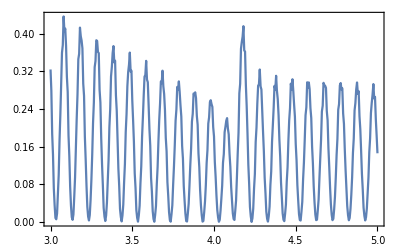

```mathematica
ListLinePlot[tk06s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/100,0]},{x,3.7,4.5,0.001}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(3.7 | 0.178039
3.701 | 0.159266
3.702 | 0.142634
3.703 | 0.12912
3.704 | 0.118677
3.705 | 0.110633
3.706 | 0.104044
3.707 | 0.0978883
3.708 | 0.0911729
3.709 | 0.0830697
3.71 | 0.073162
3.711 | 0.0617324
3.712 | 0.0498186
3.713 | 0.0387967
3.714 | 0.0297083
3.715 | 0.02287
3.716 | 0.0179745
3.717 | 0.0144267
3.718 | 0.0116251
3.719 | 0.00910952
3.72 | 0.00662352
3.721 | 0.00415011
3.722 | 0.00193005
3.723 | 0.00041265
3.724 | 0.0000734163
3.725 | 0.0011398
3.726 | 0.00343058
3.727 | 0.00646957
3.728 | 0.00976392
3.729 | 0.0130192
3.73 | 0.0162083
3.731 | 0.0195543
3.732 | 0.0234922
3.733 | 0.0286176
3.734 | 0.0355722
3.735 | 0.0448023
3.736 | 0.0562121
3.737 | 0.0689471
3.738 | 0.0816297
3.739 | 0.0930166
3.74 | 0.102563
3.741 | 0.110505
3.742 | 0.117599
3.743 | 0.124823
3.744 | 0.133207
3.745 | 0.143719
3.746 | 0.157112
3.747 | 0.17362
3.748 | 0.192566
3.749 | 0.212179
3.75 | 0.230071
3.751 | 0.244351
3.752 | 0.25454
3.753 | 0.261575
3.754 | 0.267138
3.755 | 0.272987
3.756 | 0.280618
3.757 | 0.291144
3.758 | 0.305185
3.759 | 0.32263
3.76 | 0.342294
3.761 | 0.361771
3.762 | 0.377989
3.763 | 0.38857
3.764 | 0.393093
3.765 | 0.393165
3.766 | 0.391383
3.767 | 0.390225
3.768 | 0.391511
3.769 | 0.396301
3.77 | 0.404928
3.771 | 0.416905
3.772 | 0.430719
3.773 | 0.443731
3.774 | 0.452673
3.775 | 0.45496
3.776 | 0.450137
3.777 | 0.440172
3.778 | 0.428282
3.779 | 0.417453
3.78 | 0.409645
3.781 | 0.405732
3.782 | 0.405692
3.783 | 0.408723
3.784 | 0.413207
3.785 | 0.4167
3.786 | 0.416295
3.787 | 0.409645
3.788 | 0.396275
3.789 | 0.378074
3.79 | 0.35831
3.791 | 0.340028
3.792 | 0.325088
3.793 | 0.314078
3.794 | 0.30665
3.795 | 0.301816
3.796 | 0.29808
3.797 | 0.293512
3.798 | 0.285996
3.799 | 0.273872
3.8 | 0.25684
3.801 | 0.236417
3.802 | 0.21529
3.803 | 0.195981
3.804 | 0.179913
3.805 | 0.167319
3.806 | 0.157634
3.807 | 0.149875
3.808 | 0.142869
3.809 | 0.135378
3.81 | 0.126248
3.811 | 0.114725
3.812 | 0.100872
3.813 | 0.0857706
3.814 | 0.0711231
3.815 | 0.058414
3.816 | 0.0483112
3.817 | 0.0406626
3.818 | 0.0348502
3.819 | 0.0301354
3.82 | 0.0258588
3.821 | 0.0215337
3.822 | 0.0169113
3.823 | 0.0120514
3.824 | 0.00735833
3.825 | 0.00347181
3.826 | 0.000967152
3.827 | 0.0000381502
3.828 | 0.000434087
3.829 | 0.00167655
3.83 | 0.00333246
3.831 | 0.00517342
3.832 | 0.00722062
3.833 | 0.00973765
3.834 | 0.0131988
3.835 | 0.0182021
3.836 | 0.0252642
3.837 | 0.0344917
3.838 | 0.0453144
3.839 | 0.0565973
3.84 | 0.0671784
3.841 | 0.0764188
3.842 | 0.0843673
3.843 | 0.0915915
3.844 | 0.0989401
3.845 | 0.107382
3.846 | 0.117896
3.847 | 0.131312
3.848 | 0.147999
3.849 | 0.167435
3.85 | 0.18796
3.851 | 0.207187
3.852 | 0.223096
3.853 | 0.235022
3.854 | 0.24375
3.855 | 0.250899
3.856 | 0.258259
3.857 | 0.267432
3.858 | 0.279686
3.859 | 0.295826
3.86 | 0.31591
3.861 | 0.338829
3.862 | 0.362073
3.863 | 0.382257
3.864 | 0.396581
3.865 | 0.4043
3.866 | 0.406931
3.867 | 0.407215
3.868 | 0.407909
3.869 | 0.411146
3.87 | 0.41829
3.871 | 0.429937
3.872 | 0.445777
3.873 | 0.4643
3.874 | 0.482605
3.875 | 0.496855
3.876 | 0.503753
3.877 | 0.502323
3.878 | 0.494453
3.879 | 0.483698
3.88 | 0.473579
3.881 | 0.466591
3.882 | 0.464033
3.883 | 0.466181
3.884 | 0.472381
3.885 | 0.480962
3.886 | 0.489138
3.887 | 0.493341
3.888 | 0.490378
3.889 | 0.479113
3.89 | 0.461295
3.891 | 0.440615
3.892 | 0.420831
3.893 | 0.40448
3.894 | 0.392643
3.895 | 0.385247
3.896 | 0.381385
3.897 | 0.379441
3.898 | 0.377134
3.899 | 0.371741
3.9 | 0.360846
3.901 | 0.343529
3.902 | 0.321151
3.903 | 0.29681
3.904 | 0.273749
3.905 | 0.254079
3.906 | 0.238485
3.907 | 0.226588
3.908 | 0.217387
3.909 | 0.209523
3.91 | 0.201423
3.911 | 0.191462
3.912 | 0.178359
3.913 | 0.161781
3.914 | 0.14277
3.915 | 0.123411
3.916 | 0.105805
3.917 | 0.0911633
3.918 | 0.0796271
3.919 | 0.0706202
3.92 | 0.0632723
3.921 | 0.0566896
3.922 | 0.0500927
3.923 | 0.0429172
3.924 | 0.034948
3.925 | 0.0264622
3.926 | 0.0182311
3.927 | 0.0112173
3.928 | 0.00608503
3.929 | 0.00291069
3.93 | 0.00129668
3.931 | 0.000692571
3.932 | 0.000657039
3.933 | 0.000981635
3.934 | 0.00172581
3.935 | 0.00321176
3.936 | 0.00597014
3.937 | 0.0105773
3.938 | 0.0173493
3.939 | 0.0260249
3.94 | 0.0357411
3.941 | 0.0454391
3.942 | 0.0543935
3.943 | 0.0624651
3.944 | 0.0700353
3.945 | 0.0778295
3.946 | 0.086773
3.947 | 0.0978803
3.948 | 0.112082
3.949 | 0.129887
3.95 | 0.150902
3.951 | 0.173503
3.952 | 0.195203
3.953 | 0.213783
3.954 | 0.228384
3.955 | 0.2397
3.956 | 0.249387
3.957 | 0.25938
3.958 | 0.271499
3.959 | 0.287268
3.96 | 0.307743
3.961 | 0.333147
3.962 | 0.362328
3.963 | 0.392405
3.964 | 0.419325
3.965 | 0.439578
3.966 | 0.452036
3.967 | 0.458318
3.968 | 0.461633
3.969 | 0.465345
3.97 | 0.472182
3.971 | 0.484022
3.972 | 0.501843
3.973 | 0.525505
3.974 | 0.553306
3.975 | 0.581621
3.976 | 0.605376
3.977 | 0.619933
3.978 | 0.623525
3.979 | 0.6182
3.98 | 0.608446
3.981 | 0.598972
3.982 | 0.593335
3.983 | 0.593616
3.984 | 0.60057
3.985 | 0.613699
3.986 | 0.631047
3.987 | 0.648944
3.988 | 0.662301
3.989 | 0.666142
3.99 | 0.658069
3.991 | 0.63979
3.992 | 0.616139
3.993 | 0.592521
3.994 | 0.572948
3.995 | 0.559506
3.996 | 0.55264
3.997 | 0.551535
3.998 | 0.554233
3.999 | 0.557589
4. | 0.557457
4.001 | 0.54967
4.002 | 0.531896
4.003 | 0.505193
4.004 | 0.473656
4.005 | 0.442244
4.006 | 0.414677
4.007 | 0.392689
4.008 | 0.376353
4.009 | 0.364643
4.01 | 0.355805
4.011 | 0.347517
4.012 | 0.337076
4.013 | 0.32193
4.014 | 0.300698
4.015 | 0.274149
4.016 | 0.245114
4.017 | 0.217069
4.018 | 0.192536
4.019 | 0.172452
4.02 | 0.156468
4.021 | 0.143532
4.022 | 0.13232
4.023 | 0.121471
4.024 | 0.109756
4.025 | 0.0963235
4.026 | 0.081054
4.027 | 0.0648036
4.028 | 0.049166
4.029 | 0.0357008
4.03 | 0.0252025
4.031 | 0.0175613
4.032 | 0.0121265
4.033 | 0.00814525
4.034 | 0.00504215
4.035 | 0.00254723
4.036 | 0.000747682
4.037 | 0.0000883865
4.038 | 0.00126515
4.039 | 0.00492982
4.04 | 0.0112678
4.041 | 0.0197627
4.042 | 0.0294366
4.043 | 0.0393993
4.044 | 0.0492617
4.045 | 0.0592268
4.046 | 0.0699922
4.047 | 0.0826221
4.048 | 0.0984134
4.049 | 0.11866
4.05 | 0.144186
4.051 | 0.174647
4.052 | 0.208026
4.053 | 0.241042
4.054 | 0.270661
4.055 | 0.295634
4.056 | 0.316869
4.057 | 0.336716
4.058 | 0.358068
4.059 | 0.383807
4.06 | 0.41651
4.061 | 0.458096
4.062 | 0.509115
4.063 | 0.567694
4.064 | 0.628815
4.065 | 0.68522
4.066 | 0.730516
4.067 | 0.762553
4.068 | 0.784242
4.069 | 0.801574
4.07 | 0.821072
4.071 | 0.848325
4.072 | 0.887531
4.073 | 0.941267
4.074 | 1.00984
4.075 | 1.09001
4.076 | 1.17389
4.077 | 1.24967
4.078 | 1.30583
4.079 | 1.33715
4.08 | 1.3475
4.081 | 1.34721
4.082 | 1.34798
4.083 | 1.35942
4.084 | 1.38809
4.085 | 1.43751
4.086 | 1.50802
4.087 | 1.59576
4.088 | 1.69114
4.089 | 1.77888
4.09 | 1.8419
4.091 | 1.86929
4.092 | 1.86261
4.093 | 1.83489
4.094 | 1.80342
4.095 | 1.78317
4.096 | 1.78408
4.097 | 1.81125
4.098 | 1.8655
4.099 | 1.94309
4.1 | 2.03438
4.101 | 2.12303
4.102 | 2.18839
4.103 | 2.21319
4.104 | 2.19295
4.105 | 2.13914
4.106 | 2.07252
4.107 | 2.01352
4.108 | 1.97647
4.109 | 1.96885
4.11 | 1.99252
4.111 | 2.04449
4.112 | 2.11637
4.113 | 2.19327
4.114 | 2.25446
4.115 | 2.27883
4.116 | 2.25464
4.117 | 2.18703
4.118 | 2.09552
4.119 | 2.00371
4.12 | 1.9302
4.121 | 1.88557
4.122 | 1.87336
4.123 | 1.8918
4.124 | 1.9344
4.125 | 1.98926
4.126 | 2.03878
4.127 | 2.06222
4.128 | 2.04316
4.129 | 1.97854
4.13 | 1.88148
4.131 | 1.7742
4.132 | 1.67755
4.133 | 1.60496
4.134 | 1.56214
4.135 | 1.54892
4.136 | 1.56089
4.137 | 1.58954
4.138 | 1.62192
4.139 | 1.64123
4.14 | 1.63091
4.141 | 1.58199
4.142 | 1.49897
4.143 | 1.39797
4.144 | 1.29828
4.145 | 1.21462
4.146 | 1.15458
4.147 | 1.1198
4.148 | 1.10787
4.149 | 1.11334
4.15 | 1.12779
4.151 | 1.13976
4.152 | 1.13621
4.153 | 1.10676
4.154 | 1.04922
4.155 | 0.971576
4.156 | 0.887858
4.157 | 0.811316
4.158 | 0.75027
4.159 | 0.707817
4.16 | 0.683331
4.161 | 0.673807
4.162 | 0.674395
4.163 | 0.678391
4.164 | 0.677524
4.165 | 0.66362
4.166 | 0.631892
4.167 | 0.583864
4.168 | 0.526909
4.169 | 0.470333
4.17 | 0.421379
4.171 | 0.383719
4.172 | 0.358021
4.173 | 0.343048
4.174 | 0.336395
4.175 | 0.334707
4.176 | 0.333708
4.177 | 0.328593
4.178 | 0.315313
4.179 | 0.292453
4.18 | 0.262219
4.181 | 0.229288
4.182 | 0.198409
4.183 | 0.172695
4.184 | 0.153365
4.185 | 0.140277
4.186 | 0.132512
4.187 | 0.128684
4.188 | 0.127013
4.189 | 0.125374
4.19 | 0.121575
4.191 | 0.11405
4.192 | 0.102628
4.193 | 0.0886598
4.194 | 0.0742416
4.195 | 0.0612002
4.196 | 0.0505768
4.197 | 0.0426755
4.198 | 0.0373304
4.199 | 0.0341292
4.2 | 0.0325169
4.201 | 0.0318157
4.202 | 0.0312449
4.203 | 0.0300404
4.204 | 0.0277016
4.205 | 0.0242153
4.206 | 0.0200295
4.207 | 0.0157692
4.208 | 0.0119441
4.209 | 0.00883067
4.21 | 0.00650637
4.211 | 0.00492919
4.212 | 0.00399846
4.213 | 0.00358178
4.214 | 0.00351817
4.215 | 0.00361841
4.216 | 0.00368777
4.217 | 0.00357938
4.218 | 0.0032454
4.219 | 0.00273708
4.22 | 0.00215302
4.221 | 0.00158342
4.222 | 0.0010846
4.223 | 0.000680781
4.224 | 0.000376283
4.225 | 0.00016703
4.226 | 0.0000473869
4.227 | 0.0000116316
4.228 | 0.000050438
4.229 | 0.000145181
4.23 | 0.000266213
4.231 | 0.000379427
4.232 | 0.00045688
4.233 | 0.000483115
4.234 | 0.000454871
4.235 | 0.000378212
4.236 | 0.000267134
4.237 | 0.000144652
4.238 | 0.0000447319
4.239 | 0.0000111037
4.24 | 0.0000871143
4.241 | 0.000293907
4.242 | 0.00060721
4.243 | 0.000955833
4.244 | 0.00125191
4.245 | 0.00143038
4.246 | 0.00146891
4.247 | 0.00138577
4.248 | 0.00123061
4.249 | 0.00107963
4.25 | 0.0010351
4.251 | 0.00122097
4.252 | 0.00175987
4.253 | 0.00272056
4.254 | 0.00405096
4.255 | 0.00555392
4.256 | 0.00695635
4.257 | 0.00803378
4.258 | 0.00869173
4.259 | 0.00896352
4.26 | 0.00896627
4.261 | 0.00886421
4.262 | 0.00885413
4.263 | 0.00916076
4.264 | 0.0100171
4.265 | 0.011603
4.266 | 0.0139379
4.267 | 0.0167907
4.268 | 0.0197168
4.269 | 0.0222479
4.27 | 0.0240948
4.271 | 0.0252123
4.272 | 0.0257365
4.273 | 0.0258939
4.274 | 0.0259457
4.275 | 0.0261695
4.276 | 0.0268492
4.277 | 0.0282392
4.278 | 0.0304769
4.279 | 0.0334659
4.28 | 0.0368288
4.281 | 0.0400321
4.282 | 0.0426271
4.283 | 0.0444166
4.284 | 0.0454482
4.285 | 0.0459112
4.286 | 0.0460419
4.287 | 0.0460771
4.288 | 0.0462413
4.289 | 0.0467379
4.29 | 0.0477196
4.291 | 0.0492278
4.292 | 0.051133
4.293 | 0.0531482
4.294 | 0.054947
4.295 | 0.0563068
4.296 | 0.0571648
4.297 | 0.0575773
4.298 | 0.0576475
4.299 | 0.0574747
4.3 | 0.057133
4.301 | 0.0566708
4.302 | 0.0561203
4.303 | 0.0555119
4.304 | 0.0548866
4.305 | 0.0542981
4.306 | 0.0537959
4.307 | 0.0534024
4.308 | 0.0531016
4.309 | 0.0528443
4.31 | 0.0525592
4.311 | 0.0521581
4.312 | 0.0515354
4.313 | 0.0505689
4.314 | 0.0491348
4.315 | 0.0471492
4.316 | 0.0446392
4.317 | 0.0418044
4.318 | 0.0389947
4.319 | 0.0365709
4.32 | 0.0347406
4.321 | 0.0334985
4.322 | 0.0326836
4.323 | 0.0320683
4.324 | 0.0314167
4.325 | 0.0305057
4.326 | 0.0291354
4.327 | 0.0271552
4.328 | 0.0245229
4.329 | 0.021381
4.33 | 0.0180796
4.331 | 0.0150702
4.332 | 0.0127019
4.333 | 0.0110805
4.334 | 0.010086
4.335 | 0.00948613
4.336 | 0.00903959
4.337 | 0.00854588
4.338 | 0.00786007
4.339 | 0.00689893
4.34 | 0.00565536
4.341 | 0.0042184
4.342 | 0.00277199
4.343 | 0.00153855
4.344 | 0.000676845
4.345 | 0.00020931
4.346 | 0.0000391682
4.347 | 0.0000283758
4.348 | 0.0000685118
4.349 | 0.000115158
4.35 | 0.000195835
4.351 | 0.000406656
4.352 | 0.00089876
4.353 | 0.00184043
4.354 | 0.00334012
4.355 | 0.00534961
4.356 | 0.00762352
4.357 | 0.00980659
4.358 | 0.011602
4.359 | 0.0128876
4.36 | 0.0137217
4.361 | 0.0142878
4.362 | 0.0148444
4.363 | 0.0156992
4.364 | 0.0171895
4.365 | 0.0196321
4.366 | 0.0232098
4.367 | 0.0278112
4.368 | 0.0329384
4.369 | 0.0378394
4.37 | 0.0418434
4.371 | 0.044645
4.372 | 0.0463386
4.373 | 0.0472741
4.374 | 0.047901
4.375 | 0.0486841
4.376 | 0.0500707
4.377 | 0.0524594
4.378 | 0.0561153
4.379 | 0.0610207
4.38 | 0.0667359
4.381 | 0.0724446
4.382 | 0.0772738
4.383 | 0.0806925
4.384 | 0.0826727
4.385 | 0.0835606
4.386 | 0.083852
4.387 | 0.0840388
4.388 | 0.0845471
4.389 | 0.0857175
4.39 | 0.087772
4.391 | 0.090739
4.392 | 0.0943611
4.393 | 0.0980867
4.394 | 0.101248
4.395 | 0.103363
4.396 | 0.104334
4.397 | 0.104393
4.398 | 0.103916
4.399 | 0.103264
4.4 | 0.102704
4.401 | 0.102396
4.402 | 0.102392
4.403 | 0.102625
4.404 | 0.10291
4.405 | 0.10298
4.406 | 0.102589
4.407 | 0.101641
4.408 | 0.100237
4.409 | 0.0986022
4.41 | 0.0969548
4.411 | 0.0954292
4.412 | 0.0940512
4.413 | 0.0927475
4.414 | 0.0913593
4.415 | 0.0896626
4.416 | 0.0874131
4.417 | 0.0844414
4.418 | 0.0807772
4.419 | 0.0767146
4.42 | 0.0727143
4.421 | 0.0691884
4.422 | 0.0663364
4.423 | 0.0641279
4.424 | 0.0623765
4.425 | 0.0608155
4.426 | 0.0591411
4.427 | 0.0570356
4.428 | 0.0542071
4.429 | 0.050474
4.43 | 0.0458923
4.431 | 0.0408373
4.432 | 0.0359136
4.433 | 0.0316899
4.434 | 0.0284553
4.435 | 0.0261729
4.436 | 0.0245953
4.437 | 0.0234019
4.438 | 0.0222808
4.439 | 0.0209611
4.44 | 0.0192292
4.441 | 0.0169618
4.442 | 0.0141822
4.443 | 0.0111069
4.444 | 0.00810965
4.445 | 0.00557061
4.446 | 0.0037033
4.447 | 0.00249713
4.448 | 0.00179251
4.449 | 0.0013945
4.45 | 0.00114967
4.451 | 0.000976955
4.452 | 0.000872206
4.453 | 0.000900174
4.454 | 0.00117089
4.455 | 0.00178898
4.456 | 0.00278
4.457 | 0.00403905
4.458 | 0.00535981
4.459 | 0.00653666
4.46 | 0.00745869
4.461 | 0.00813963
4.462 | 0.00869975
4.463 | 0.0093396
4.464 | 0.0103223
4.465 | 0.0119525
4.466 | 0.014523
4.467 | 0.0181992
4.468 | 0.0228619
4.469 | 0.0280194
4.47 | 0.0329394
4.471 | 0.0369746
4.472 | 0.0398367
4.473 | 0.0416315
4.474 | 0.0427206
4.475 | 0.0435728
4.476 | 0.0446809
4.477 | 0.0465273
4.478 | 0.0495432
4.479 | 0.0540073
4.48 | 0.0598732
4.481 | 0.0666168
4.482 | 0.0732984
4.483 | 0.0789315
4.484 | 0.0829307
4.485 | 0.0852874
4.486 | 0.0864198
4.487 | 0.0869203
4.488 | 0.087381
4.489 | 0.0883236
4.49 | 0.0901727
4.491 | 0.0932072
4.492 | 0.0974561
4.493 | 0.102574
4.494 | 0.107827
4.495 | 0.112328
4.496 | 0.115434
4.497 | 0.117009
4.498 | 0.117364
4.499 | 0.11701
4.5 | 0.116455)

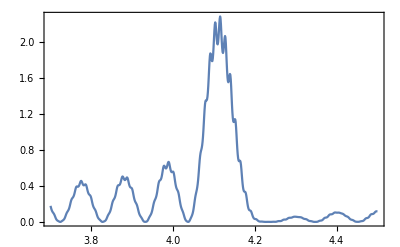

```mathematica
ListLinePlot[tk07sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/100,0]},{x,3.7,4.5,0.001}](*нужно еще посмотреть обыкновенную волну*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(3.7 | 0.23736
3.701 | 0.221798
3.702 | 0.207132
3.703 | 0.194827
3.704 | 0.185364
3.705 | 0.178472
3.706 | 0.173424
3.707 | 0.169213
3.708 | 0.164644
3.709 | 0.158448
3.71 | 0.149588
3.711 | 0.13774
3.712 | 0.123676
3.713 | 0.109065
3.714 | 0.0956636
3.715 | 0.0845621
3.716 | 0.0759737
3.717 | 0.0694861
3.718 | 0.0643956
3.719 | 0.0599272
3.72 | 0.0553445
3.721 | 0.0500288
3.722 | 0.0436056
3.723 | 0.0361228
3.724 | 0.0281562
3.725 | 0.0206422
3.726 | 0.0144348
3.727 | 0.00991161
3.728 | 0.0069283
3.729 | 0.00504624
3.73 | 0.00378713
3.731 | 0.00278422
3.732 | 0.00184449
3.733 | 0.00097257
3.734 | 0.00037798
3.735 | 0.000438873
3.736 | 0.00156838
3.737 | 0.00398502
3.738 | 0.00753114
3.739 | 0.0117247
3.74 | 0.0160203
3.741 | 0.0200556
3.742 | 0.0237412
3.743 | 0.027233
3.744 | 0.0308757
3.745 | 0.035155
3.746 | 0.0406347
3.747 | 0.0478214
3.748 | 0.0569173
3.749 | 0.0675507
3.75 | 0.0787392
3.751 | 0.0892782
3.752 | 0.098326
3.753 | 0.105718
3.754 | 0.111868
3.755 | 0.117493
3.756 | 0.123393
3.757 | 0.130339
3.758 | 0.13898
3.759 | 0.149703
3.76 | 0.16239
3.761 | 0.176187
3.762 | 0.189566
3.763 | 0.200905
3.764 | 0.209296
3.765 | 0.214919
3.766 | 0.218765
3.767 | 0.222084
3.768 | 0.226005
3.769 | 0.231374
3.77 | 0.238702
3.771 | 0.248078
3.772 | 0.259006
3.773 | 0.270262
3.774 | 0.280033
3.775 | 0.286569
3.776 | 0.289093
3.777 | 0.288214
3.778 | 0.285496
3.779 | 0.282645
3.78 | 0.280969
3.781 | 0.281219
3.782 | 0.283626
3.783 | 0.287923
3.784 | 0.293295
3.785 | 0.298328
3.786 | 0.301189
3.787 | 0.30023
3.788 | 0.294876
3.789 | 0.286061
3.79 | 0.275749
3.791 | 0.265935
3.792 | 0.25796
3.793 | 0.252374
3.794 | 0.249086
3.795 | 0.247531
3.796 | 0.246731
3.797 | 0.245329
3.798 | 0.241751
3.799 | 0.234672
3.8 | 0.223724
3.801 | 0.20991
3.802 | 0.195207
3.803 | 0.181582
3.804 | 0.170236
3.805 | 0.161473
3.806 | 0.154948
3.807 | 0.149942
3.808 | 0.14552
3.809 | 0.140616
3.81 | 0.134154
3.811 | 0.125324
3.812 | 0.114002
3.813 | 0.101026
3.814 | 0.0879332
3.815 | 0.0762146
3.816 | 0.0666904
3.817 | 0.0594044
3.818 | 0.0538925
3.819 | 0.0494869
3.82 | 0.0455042
3.821 | 0.0413354
3.822 | 0.0365146
3.823 | 0.0308251
3.824 | 0.0244319
3.825 | 0.017921
3.826 | 0.0120974
3.827 | 0.00759171
3.828 | 0.00457808
3.829 | 0.00281049
3.83 | 0.0018573
3.831 | 0.00131711
3.832 | 0.000931147
3.833 | 0.000621876
3.834 | 0.000502606
3.835 | 0.000865859
3.836 | 0.00211512
3.837 | 0.0045958
3.838 | 0.00836355
3.839 | 0.0130663
3.84 | 0.0180939
3.841 | 0.0228907
3.842 | 0.027178
3.843 | 0.0309878
3.844 | 0.0345931
3.845 | 0.0384339
3.846 | 0.0430622
3.847 | 0.0490699
3.848 | 0.056934
3.849 | 0.0667523
3.85 | 0.0779828
3.851 | 0.0894725
3.852 | 0.0999348
3.853 | 0.108573
3.854 | 0.115348
3.855 | 0.120813
3.856 | 0.125788
3.857 | 0.131138
3.858 | 0.137656
3.859 | 0.145984
3.86 | 0.156467
3.861 | 0.168904
3.862 | 0.182332
3.863 | 0.195126
3.864 | 0.205631
3.865 | 0.212993
3.866 | 0.217492
3.867 | 0.220205
3.868 | 0.222432
3.869 | 0.225305
3.87 | 0.229651
3.871 | 0.235952
3.872 | 0.244261
3.873 | 0.254058
3.874 | 0.264112
3.875 | 0.272642
3.876 | 0.277966
3.877 | 0.279382
3.878 | 0.277532
3.879 | 0.273951
3.88 | 0.270275
3.881 | 0.267732
3.882 | 0.267003
3.883 | 0.268273
3.884 | 0.271257
3.885 | 0.275169
3.886 | 0.278685
3.887 | 0.280127
3.888 | 0.278041
3.889 | 0.271987
3.89 | 0.262905
3.891 | 0.252611
3.892 | 0.24289
3.893 | 0.234893
3.894 | 0.229046
3.895 | 0.225206
3.896 | 0.222811
3.897 | 0.22095
3.898 | 0.218407
3.899 | 0.213826
3.9 | 0.206145
3.901 | 0.195195
3.902 | 0.181999
3.903 | 0.168343
3.904 | 0.155888
3.905 | 0.145566
3.906 | 0.137517
3.907 | 0.131345
3.908 | 0.12636
3.909 | 0.121722
3.91 | 0.116519
3.911 | 0.109883
3.912 | 0.101244
3.913 | 0.0906676
3.914 | 0.0790184
3.915 | 0.0676539
3.916 | 0.0577641
3.917 | 0.0498942
3.918 | 0.0439359
3.919 | 0.0393989
3.92 | 0.0356764
3.921 | 0.032197
3.922 | 0.0284955
3.923 | 0.0242693
3.924 | 0.01946
3.925 | 0.0143327
3.926 | 0.00944988
3.927 | 0.00544599
3.928 | 0.0027051
3.929 | 0.00120212
3.93 | 0.000613014
3.931 | 0.000540917
3.932 | 0.000683976
3.933 | 0.000906231
3.934 | 0.00125315
3.935 | 0.00194629
3.936 | 0.00335045
3.937 | 0.00587111
3.938 | 0.0097532
3.939 | 0.0148608
3.94 | 0.02064
3.941 | 0.0263712
3.942 | 0.0315203
3.943 | 0.0359206
3.944 | 0.0397423
3.945 | 0.043382
3.946 | 0.0473728
3.947 | 0.0523244
3.948 | 0.05884
3.949 | 0.0673436
3.95 | 0.0778006
3.951 | 0.0894809
3.952 | 0.101065
3.953 | 0.111212
3.954 | 0.119204
3.955 | 0.125154
3.956 | 0.129757
3.957 | 0.133938
3.958 | 0.13861
3.959 | 0.14458
3.96 | 0.152467
3.961 | 0.162555
3.962 | 0.174551
3.963 | 0.187378
3.964 | 0.19933
3.965 | 0.208749
3.966 | 0.21486
3.967 | 0.218051
3.968 | 0.219479
3.969 | 0.22047
3.97 | 0.222148
3.971 | 0.22531
3.972 | 0.230395
3.973 | 0.237421
3.974 | 0.245846
3.975 | 0.254455
3.976 | 0.261529
3.977 | 0.265488
3.978 | 0.265711
3.979 | 0.262858
3.98 | 0.2584
3.981 | 0.25387
3.982 | 0.250393
3.983 | 0.248573
3.984 | 0.248549
3.985 | 0.250033
3.986 | 0.252287
3.987 | 0.254114
3.988 | 0.254041
3.989 | 0.25084
3.99 | 0.244215
3.991 | 0.235061
3.992 | 0.224988
3.993 | 0.215517
3.994 | 0.207587
3.995 | 0.201499
3.996 | 0.197067
3.997 | 0.193757
3.998 | 0.190759
3.999 | 0.187042
4. | 0.18152
4.001 | 0.173427
4.002 | 0.162793
4.003 | 0.150608
4.004 | 0.138385
4.005 | 0.127422
4.006 | 0.118352
4.007 | 0.111164
4.008 | 0.10543
4.009 | 0.100523
4.01 | 0.0957329
4.011 | 0.0903402
4.012 | 0.0837273
4.013 | 0.0755859
4.014 | 0.0661579
4.015 | 0.0562841
4.016 | 0.047069
4.017 | 0.0393455
4.018 | 0.0333691
4.019 | 0.0288968
4.02 | 0.0254449
4.021 | 0.0225026
4.022 | 0.0196419
4.023 | 0.0165675
4.024 | 0.0131574
4.025 | 0.00951128
4.026 | 0.00596975
4.027 | 0.0030212
4.028 | 0.00107433
4.029 | 0.000236737
4.03 | 0.000291176
4.031 | 0.00086783
4.032 | 0.00164164
4.033 | 0.00243971
4.034 | 0.00326709
4.035 | 0.0042988
4.036 | 0.00585837
4.037 | 0.00836124
4.038 | 0.0121778
4.039 | 0.0174096
4.04 | 0.0237014
4.041 | 0.0303035
4.042 | 0.0364236
4.043 | 0.0415933
4.044 | 0.0457882
4.045 | 0.0493272
4.046 | 0.052724
4.047 | 0.0565862
4.048 | 0.0615525
4.049 | 0.0682026
4.05 | 0.0768719
4.051 | 0.0873745
4.052 | 0.0988082
4.053 | 0.109743
4.054 | 0.118854
4.055 | 0.125547
4.056 | 0.130086
4.057 | 0.13328
4.058 | 0.136105
4.059 | 0.139475
4.06 | 0.14416
4.061 | 0.150713
4.062 | 0.159344
4.063 | 0.169688
4.064 | 0.180641
4.065 | 0.190545
4.066 | 0.197861
4.067 | 0.201932
4.068 | 0.2032
4.069 | 0.202787
4.07 | 0.201932
4.071 | 0.20165
4.072 | 0.202634
4.073 | 0.205247
4.074 | 0.209479
4.075 | 0.214845
4.076 | 0.22031
4.077 | 0.224448
4.078 | 0.225975
4.079 | 0.224414
4.08 | 0.220318
4.081 | 0.214873
4.082 | 0.209284
4.083 | 0.204409
4.084 | 0.200684
4.085 | 0.198172
4.086 | 0.196624
4.087 | 0.195483
4.088 | 0.193913
4.089 | 0.190962
4.09 | 0.18592
4.091 | 0.178735
4.092 | 0.170103
4.093 | 0.161086
4.094 | 0.152596
4.095 | 0.145115
4.096 | 0.138702
4.097 | 0.133125
4.098 | 0.127964
4.099 | 0.12269
4.1 | 0.116738
4.101 | 0.109653
4.102 | 0.101304
4.103 | 0.0920648
4.104 | 0.0827207
4.105 | 0.0740952
4.106 | 0.0666674
4.107 | 0.0604665
4.108 | 0.0552068
4.109 | 0.0504746
4.11 | 0.0458552
4.111 | 0.0410051
4.112 | 0.0357092
4.113 | 0.0299557
4.114 | 0.024009
4.115 | 0.0183954
4.116 | 0.0137121
4.117 | 0.0103251
4.118 | 0.00819538
4.119 | 0.00697063
4.12 | 0.00621606
4.121 | 0.00559639
4.122 | 0.00495303
4.123 | 0.00431876
4.124 | 0.00391368
4.125 | 0.00412495
4.126 | 0.00542924
4.127 | 0.00820931
4.128 | 0.0125
4.129 | 0.0178536
4.13 | 0.0235139
4.131 | 0.0288024
4.132 | 0.0334048
4.133 | 0.0374134
4.134 | 0.0412249
4.135 | 0.0454305
4.136 | 0.0507382
4.137 | 0.0578828
4.138 | 0.0674444
4.139 | 0.079534
4.14 | 0.0934609
4.141 | 0.107723
4.142 | 0.120581
4.143 | 0.130907
4.144 | 0.138629
4.145 | 0.144548
4.146 | 0.14988
4.147 | 0.155909
4.148 | 0.163821
4.149 | 0.174602
4.15 | 0.188849
4.151 | 0.206423
4.152 | 0.226064
4.153 | 0.245376
4.154 | 0.261619
4.155 | 0.273024
4.156 | 0.279609
4.157 | 0.282887
4.158 | 0.284972
4.159 | 0.287866
4.16 | 0.293154
4.161 | 0.301926
4.162 | 0.314683
4.163 | 0.331087
4.164 | 0.349614
4.165 | 0.367492
4.166 | 0.381424
4.167 | 0.389075
4.168 | 0.390292
4.169 | 0.386975
4.17 | 0.38191
4.171 | 0.377646
4.172 | 0.376
4.173 | 0.378001
4.174 | 0.383936
4.175 | 0.393282
4.176 | 0.404504
4.177 | 0.415
4.178 | 0.421621
4.179 | 0.421946
4.18 | 0.415605
4.181 | 0.404459
4.182 | 0.39147
4.183 | 0.379358
4.184 | 0.369908
4.185 | 0.363924
4.186 | 0.361405
4.187 | 0.361656
4.188 | 0.363271
4.189 | 0.364153
4.19 | 0.361853
4.191 | 0.354453
4.192 | 0.341624
4.193 | 0.324939
4.194 | 0.307028
4.195 | 0.290301
4.196 | 0.276206
4.197 | 0.265189
4.198 | 0.256957
4.199 | 0.25071
4.2 | 0.245263
4.201 | 0.239136
4.202 | 0.230783
4.203 | 0.219099
4.204 | 0.204059
4.205 | 0.186925
4.206 | 0.169675
4.207 | 0.154033
4.208 | 0.140875
4.209 | 0.130239
4.21 | 0.121625
4.211 | 0.114268
4.212 | 0.107309
4.213 | 0.0998938
4.214 | 0.0913096
4.215 | 0.0812181
4.216 | 0.0699023
4.217 | 0.0582862
4.218 | 0.0475459
4.219 | 0.0385381
4.22 | 0.0314976
4.221 | 0.0261416
4.222 | 0.0219509
4.223 | 0.0183992
4.224 | 0.0150734
4.225 | 0.0117284
4.226 | 0.00832519
4.227 | 0.0050567
4.228 | 0.00231704
4.229 | 0.000550594
4.23 | 0.000012204
4.231 | 0.00061342
4.232 | 0.00199701
4.233 | 0.00375903
4.234 | 0.00563363
4.235 | 0.00756469
4.236 | 0.00970275
4.237 | 0.0123769
4.238 | 0.0160474
4.239 | 0.0212014
4.24 | 0.0281479
4.241 | 0.0367485
4.242 | 0.0462804
4.243 | 0.0556644
4.244 | 0.063981
4.245 | 0.0708713
4.246 | 0.0765686
4.247 | 0.081691
4.248 | 0.0870279
4.249 | 0.0934095
4.25 | 0.101616
4.251 | 0.112234
4.252 | 0.125394
4.253 | 0.140453
4.254 | 0.155887
4.255 | 0.169742
4.256 | 0.180545
4.257 | 0.18798
4.258 | 0.19284
4.259 | 0.196478
4.26 | 0.200304
4.261 | 0.205524
4.262 | 0.21305
4.263 | 0.223399
4.264 | 0.236497
4.265 | 0.251402
4.266 | 0.266203
4.267 | 0.278491
4.268 | 0.28641
4.269 | 0.289596
4.27 | 0.28921
4.271 | 0.287162
4.272 | 0.285308
4.273 | 0.285043
4.274 | 0.287218
4.275 | 0.292149
4.276 | 0.299546
4.277 | 0.308365
4.278 | 0.316757
4.279 | 0.322432
4.28 | 0.323572
4.281 | 0.319807
4.282 | 0.312375
4.283 | 0.303362
4.284 | 0.294734
4.285 | 0.28782
4.286 | 0.283245
4.287 | 0.281042
4.288 | 0.280723
4.289 | 0.281277
4.29 | 0.281199
4.291 | 0.278756
4.292 | 0.272622
4.293 | 0.262615
4.294 | 0.24989
4.295 | 0.236314
4.296 | 0.223575
4.297 | 0.21267
4.298 | 0.203877
4.299 | 0.196945
4.3 | 0.191264
4.301 | 0.185961
4.302 | 0.179988
4.303 | 0.172313
4.304 | 0.162291
4.305 | 0.150072
4.306 | 0.136671
4.307 | 0.123497
4.308 | 0.111681
4.309 | 0.101716
4.31 | 0.0935137
4.311 | 0.0866337
4.312 | 0.0804873
4.313 | 0.0744578
4.314 | 0.0679851
4.315 | 0.0606755
4.316 | 0.0524598
4.317 | 0.0437196
4.318 | 0.0352122
4.319 | 0.0277332
4.32 | 0.0217375
4.321 | 0.0172119
4.322 | 0.0138235
4.323 | 0.0111446
4.324 | 0.00880992
4.325 | 0.00659014
4.326 | 0.0044227
4.327 | 0.00242639
4.328 | 0.000888911
4.329 | 0.000183173
4.33 | 0.000590323
4.331 | 0.00211373
4.332 | 0.00444797
4.333 | 0.00715111
4.334 | 0.0098713
4.335 | 0.0124725
4.336 | 0.0150455
4.337 | 0.0178697
4.338 | 0.0213677
4.339 | 0.0260431
4.34 | 0.0323556
4.341 | 0.0405005
4.342 | 0.0501566
4.343 | 0.060421
4.344 | 0.070131
4.345 | 0.0784187
4.346 | 0.085068
4.347 | 0.0904716
4.348 | 0.0953734
4.349 | 0.100638
4.35 | 0.10712
4.351 | 0.11557
4.352 | 0.126486
4.353 | 0.139853
4.354 | 0.154854
4.355 | 0.169842
4.356 | 0.182863
4.357 | 0.192574
4.358 | 0.198843
4.359 | 0.202616
4.36 | 0.205328
4.361 | 0.20841
4.362 | 0.213038
4.363 | 0.220054
4.364 | 0.229876
4.365 | 0.242306
4.366 | 0.256285
4.367 | 0.269856
4.368 | 0.280672
4.369 | 0.28704
4.37 | 0.288769
4.371 | 0.287111
4.372 | 0.283984
4.373 | 0.281197
4.374 | 0.28007
4.375 | 0.281374
4.376 | 0.285342
4.377 | 0.291615
4.378 | 0.299117
4.379 | 0.306039
4.38 | 0.310222
4.381 | 0.31003
4.382 | 0.305217
4.383 | 0.297032
4.384 | 0.287462
4.385 | 0.278345
4.386 | 0.270897
4.387 | 0.265667
4.388 | 0.262641
4.389 | 0.261323
4.39 | 0.260747
4.391 | 0.259523
4.392 | 0.2561
4.393 | 0.249345
4.394 | 0.239168
4.395 | 0.226653
4.396 | 0.213478
4.397 | 0.201127
4.398 | 0.190452
4.399 | 0.181667
4.4 | 0.174516
4.401 | 0.168433
4.402 | 0.162642
4.403 | 0.156246
4.404 | 0.148404
4.405 | 0.138649
4.406 | 0.127197
4.407 | 0.114953
4.408 | 0.103092
4.409 | 0.0925062
4.41 | 0.0835402
4.411 | 0.0760599
4.412 | 0.0696584
4.413 | 0.0638293
4.414 | 0.0580725
4.415 | 0.0519712
4.416 | 0.0452856
4.417 | 0.0380669
4.418 | 0.0307178
4.419 | 0.0238762
4.42 | 0.0181197
4.421 | 0.0136948
4.422 | 0.0104763
4.423 | 0.008127
4.424 | 0.00628691
4.425 | 0.00469201
4.426 | 0.00322401
4.427 | 0.00192658
4.428 | 0.00100309
4.429 | 0.00077605
4.43 | 0.0015716
4.431 | 0.00353707
4.432 | 0.00650429
4.433 | 0.0100418
4.434 | 0.0136796
4.435 | 0.017125
4.436 | 0.0203444
4.437 | 0.0235344
4.438 | 0.0270618
4.439 | 0.0314055
4.44 | 0.0370812
4.441 | 0.0445008
4.442 | 0.0537446
4.443 | 0.0643346
4.444 | 0.0752364
4.445 | 0.0852501
4.446 | 0.0935795
4.447 | 0.100142
4.448 | 0.105463
4.449 | 0.110389
4.45 | 0.115836
4.451 | 0.122668
4.452 | 0.131592
4.453 | 0.143005
4.454 | 0.156741
4.455 | 0.17182
4.456 | 0.186491
4.457 | 0.198824
4.458 | 0.207617
4.459 | 0.212924
4.46 | 0.215838
4.461 | 0.217877
4.462 | 0.220487
4.463 | 0.224813
4.464 | 0.231624
4.465 | 0.241225
4.466 | 0.253277
4.467 | 0.266588
4.468 | 0.279133
4.469 | 0.288624
4.47 | 0.29353
4.471 | 0.293846
4.472 | 0.29095
4.473 | 0.2868
4.474 | 0.28318
4.475 | 0.281351
4.476 | 0.282006
4.477 | 0.285286
4.478 | 0.290736
4.479 | 0.29721
4.48 | 0.302889
4.481 | 0.3057
4.482 | 0.304157
4.483 | 0.29816
4.484 | 0.289011
4.485 | 0.278676
4.486 | 0.268921
4.487 | 0.260885
4.488 | 0.255049
4.489 | 0.251345
4.49 | 0.249245
4.491 | 0.247784
4.492 | 0.245625
4.493 | 0.241328
4.494 | 0.233892
4.495 | 0.223311
4.496 | 0.210647
4.497 | 0.197476
4.498 | 0.185162
4.499 | 0.174471
4.5 | 0.16557)

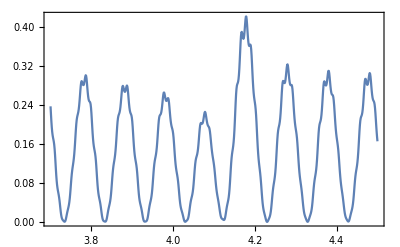

```mathematica
ListLinePlot[tk07s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk06sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/100,0]},{x,3,5,0.005}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(3. | 0.0141261
3.005 | 0.0515555
3.01 | 0.0892688
3.015 | 0.132283
3.02 | 0.202389
3.025 | 0.232868
3.03 | 0.301979
3.035 | 0.320884
3.04 | 0.352936
3.045 | 0.361828
3.05 | 0.343544
3.055 | 0.341166
3.06 | 0.278636
3.065 | 0.257016
3.07 | 0.186901
3.075 | 0.13892
3.08 | 0.0966288
3.085 | 0.0418853
3.09 | 0.0229774
3.095 | 0.0028148
3.1 | 0.00213506
3.105 | 0.0199481
3.11 | 0.0540502
3.115 | 0.0841119
3.12 | 0.152805
3.125 | 0.187443
3.13 | 0.251898
3.135 | 0.293532
3.14 | 0.322661
3.145 | 0.360932
3.15 | 0.34586
3.155 | 0.36234
3.16 | 0.313603
3.165 | 0.291921
3.17 | 0.241914
3.175 | 0.180141
3.18 | 0.146128
3.185 | 0.0764986
3.19 | 0.0492823
3.195 | 0.0158634
3.2 | 0.00109549
3.205 | 0.00343492
3.21 | 0.0259383
3.215 | 0.0472248
3.22 | 0.10352
3.225 | 0.145012
3.23 | 0.198352
3.235 | 0.260261
3.24 | 0.287705
3.245 | 0.346167
3.25 | 0.34313
3.255 | 0.368127
3.26 | 0.345605
3.265 | 0.319482
3.27 | 0.295401
3.275 | 0.224085
3.28 | 0.196337
3.285 | 0.122384
3.29 | 0.0828136
3.295 | 0.0441688
3.3 | 0.0107708
3.305 | 0.00222218
3.31 | 0.00713308
3.315 | 0.0213944
3.32 | 0.0595771
3.325 | 0.105551
3.33 | 0.147309
3.335 | 0.220432
3.34 | 0.250974
3.345 | 0.317116
3.35 | 0.335259
3.355 | 0.360698
3.36 | 0.370955
3.365 | 0.341214
3.37 | 0.34057
3.375 | 0.270882
3.38 | 0.243308
3.385 | 0.178433
3.39 | 0.122274
3.395 | 0.0850827
3.4 | 0.0319758
3.405 | 0.0142014
3.41 | 0.000720431
3.415 | 0.00579171
3.42 | 0.0261042
3.425 | 0.0694245
3.43 | 0.102669
3.435 | 0.174976
3.44 | 0.213841
3.445 | 0.276983
3.45 | 0.321177
3.455 | 0.344039
3.46 | 0.384972
3.465 | 0.358647
3.47 | 0.372679
3.475 | 0.319841
3.48 | 0.285887
3.485 | 0.240883
3.49 | 0.167761
3.495 | 0.133836
3.5 | 0.0661871
3.505 | 0.0368244
3.51 | 0.00941221
3.515 | 0.0000698745
3.52 | 0.00614555
3.525 | 0.0380076
3.53 | 0.0659543
3.535 | 0.127172
3.54 | 0.176668
3.545 | 0.231343
3.55 | 0.299314
3.555 | 0.322038
3.56 | 0.384041
3.565 | 0.372779
3.57 | 0.3912
3.575 | 0.368828
3.58 | 0.325321
3.585 | 0.30382
3.59 | 0.220458
3.595 | 0.186133
3.6 | 0.114731
3.605 | 0.068696
3.61 | 0.0339991
3.615 | 0.00499492
3.62 | 0.0000191812
3.625 | 0.0139995
3.63 | 0.0372227
3.635 | 0.0821199
3.64 | 0.139469
3.645 | 0.185677
3.65 | 0.268622
3.655 | 0.297626
3.66 | 0.368185
3.665 | 0.384054
3.67 | 0.399717
3.675 | 0.414523
3.68 | 0.364697
3.685 | 0.36221
3.69 | 0.282532
3.695 | 0.240749
3.7 | 0.178039
3.705 | 0.110633
3.71 | 0.073162
3.715 | 0.02287
3.72 | 0.00662352
3.725 | 0.0011398
3.73 | 0.0162083
3.735 | 0.0448023
3.74 | 0.102563
3.745 | 0.143719
3.75 | 0.230071
3.755 | 0.272987
3.76 | 0.342294
3.765 | 0.393165
3.77 | 0.404928
3.775 | 0.45496
3.78 | 0.409645
3.785 | 0.4167
3.79 | 0.35831
3.795 | 0.301816
3.8 | 0.25684
3.805 | 0.167319
3.81 | 0.126248
3.815 | 0.058414
3.82 | 0.0258588
3.825 | 0.00347181
3.83 | 0.00333246
3.835 | 0.0182021
3.84 | 0.0671784
3.845 | 0.107382
3.85 | 0.18796
3.855 | 0.250899
3.86 | 0.31591
3.865 | 0.4043
3.87 | 0.41829
3.875 | 0.496855
3.88 | 0.473579
3.885 | 0.480962
3.89 | 0.461295
3.895 | 0.385247
3.9 | 0.360846
3.905 | 0.254079
3.91 | 0.201423
3.915 | 0.123411
3.92 | 0.0632723
3.925 | 0.0264622
3.93 | 0.00129668
3.935 | 0.00321176
3.94 | 0.0357411
3.945 | 0.0778295
3.95 | 0.150902
3.955 | 0.2397
3.96 | 0.307743
3.965 | 0.439578
3.97 | 0.472182
3.975 | 0.581621
3.98 | 0.608446
3.985 | 0.613699
3.99 | 0.658069
3.995 | 0.559506
4. | 0.557457
4.005 | 0.442244
4.01 | 0.355805
4.015 | 0.274149
4.02 | 0.156468
4.025 | 0.0963235
4.03 | 0.0252025
4.035 | 0.00254723
4.04 | 0.0112678
4.045 | 0.0592268
4.05 | 0.144186
4.055 | 0.295634
4.06 | 0.41651
4.065 | 0.68522
4.07 | 0.821072
4.075 | 1.09001
4.08 | 1.3475
4.085 | 1.43751
4.09 | 1.8419
4.095 | 1.78317
4.1 | 2.03438
4.105 | 2.13914
4.11 | 1.99252
4.115 | 2.27883
4.12 | 1.9302
4.125 | 1.98926
4.13 | 1.88148
4.135 | 1.54892
4.14 | 1.63091
4.145 | 1.21462
4.15 | 1.12779
4.155 | 0.971576
4.16 | 0.683331
4.165 | 0.66362
4.17 | 0.421379
4.175 | 0.334707
4.18 | 0.262219
4.185 | 0.140277
4.19 | 0.121575
4.195 | 0.0612002
4.2 | 0.0325169
4.205 | 0.0242153
4.21 | 0.00650637
4.215 | 0.00361841
4.22 | 0.00215302
4.225 | 0.00016703
4.23 | 0.000266213
4.235 | 0.000378212
4.24 | 0.0000871143
4.245 | 0.00143038
4.25 | 0.0010351
4.255 | 0.00555392
4.26 | 0.00896627
4.265 | 0.011603
4.27 | 0.0240948
4.275 | 0.0261695
4.28 | 0.0368288
4.285 | 0.0459112
4.29 | 0.0477196
4.295 | 0.0563068
4.3 | 0.057133
4.305 | 0.0542981
4.31 | 0.0525592
4.315 | 0.0471492
4.32 | 0.0347406
4.325 | 0.0305057
4.33 | 0.0180796
4.335 | 0.00948613
4.34 | 0.00565536
4.345 | 0.00020931
4.35 | 0.000195835
4.355 | 0.00534961
4.36 | 0.0137217
4.365 | 0.0196321
4.37 | 0.0418434
4.375 | 0.0486841
4.38 | 0.0667359
4.385 | 0.0835606
4.39 | 0.087772
4.395 | 0.103363
4.4 | 0.102704
4.405 | 0.10298
4.41 | 0.0969548
4.415 | 0.0896626
4.42 | 0.0727143
4.425 | 0.0608155
4.43 | 0.0458923
4.435 | 0.0261729
4.44 | 0.0192292
4.445 | 0.00557061
4.45 | 0.00114967
4.455 | 0.00178898
4.46 | 0.00745869
4.465 | 0.0119525
4.47 | 0.0329394
4.475 | 0.0435728
4.48 | 0.0598732
4.485 | 0.0852874
4.49 | 0.0901727
4.495 | 0.112328
4.5 | 0.116455
4.505 | 0.1197
4.51 | 0.119762
4.515 | 0.112608
4.52 | 0.100628
4.525 | 0.0850651
4.53 | 0.0725859
4.535 | 0.0471131
4.54 | 0.0372329
4.545 | 0.0196728
4.55 | 0.00757348
4.555 | 0.00456487
4.56 | 0.00258514
4.565 | 0.00417473
4.57 | 0.0179797
4.575 | 0.0299523
4.58 | 0.0410126
4.585 | 0.0700849
4.59 | 0.0767208
4.595 | 0.0994789
4.6 | 0.112921
4.605 | 0.116938
4.61 | 0.126955
4.615 | 0.122415
4.62 | 0.11777
4.625 | 0.104061
4.63 | 0.0949463
4.635 | 0.0706866
4.64 | 0.057452
4.645 | 0.0412017
4.65 | 0.0204117
4.655 | 0.0151355
4.66 | 0.00478311
4.665 | 0.00152023
4.67 | 0.00729154
4.675 | 0.0160117
4.68 | 0.0221126
4.685 | 0.047697
4.69 | 0.0573802
4.695 | 0.0755866
4.7 | 0.0984585
4.705 | 0.103082
4.71 | 0.120958
4.715 | 0.12269
4.72 | 0.123905
4.725 | 0.117502
4.73 | 0.111495
4.735 | 0.0943396
4.74 | 0.0783973
4.745 | 0.0667516
4.75 | 0.0398729
4.755 | 0.0321518
4.76 | 0.0168432
4.765 | 0.00583156
4.77 | 0.00575284
4.775 | 0.00663503
4.78 | 0.00860123
4.785 | 0.0256019
4.79 | 0.0372217
4.795 | 0.04922
4.8 | 0.0768911
4.805 | 0.0837681
4.81 | 0.104341
4.815 | 0.115456
4.82 | 0.12036
4.825 | 0.124405
4.83 | 0.121913
4.835 | 0.114695
4.84 | 0.0988999
4.845 | 0.0923422
4.85 | 0.0653022
4.855 | 0.0536636
4.86 | 0.0386642
4.865 | 0.0179468
4.87 | 0.0141755
4.875 | 0.00561959
4.88 | 0.00258697
4.885 | 0.0100495
4.89 | 0.019541
4.895 | 0.0263883
4.9 | 0.0519908
4.905 | 0.0626191
4.91 | 0.0811704
4.915 | 0.102018
4.92 | 0.109619
4.925 | 0.123699
4.93 | 0.126408
4.935 | 0.128569
4.94 | 0.117698
4.945 | 0.114805
4.95 | 0.0945323
4.955 | 0.0779366
4.96 | 0.0671877
4.965 | 0.0382248
4.97 | 0.0308779
4.975 | 0.0155046
4.98 | 0.00473564
4.985 | 0.00483757
4.99 | 0.00719927
4.995 | 0.0102603
5. | 0.0282839)

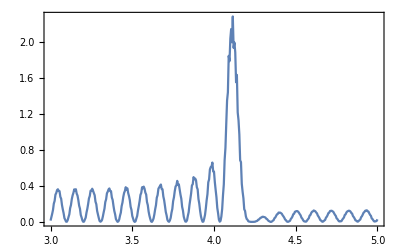

```mathematica
ListLinePlot[tk06sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
ll3ts1=AmplTwistTab[1,4.14/mee,4.14/mee/100];(*смещение на 0.02 эВ оказывается существенным для распределения по m*)
ll3tsm1=AmplTwistTab[-1,4.14/mee,4.14/mee/100];
```

```mathematica
tm3s1=Table[{m,dProbabTwist[m,ll3ts1[[3]]]},{m,-mMax,mMax}];
tm3sm1=Table[{m,dProbabTwist[m,ll3tsm1[[3]]]},{m,-mMax,mMax}];
```

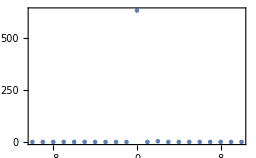
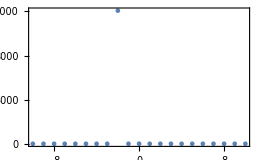

```mathematica
{ListPlot[tm3s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm3sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*старое*)
```

```mathematica
tk08s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/2,0]},{x,3.3,3.6,0.001}]
```

(3.3 | 311.442
3.301 | 286.03
3.302 | 262.908
3.303 | 242.192
3.304 | 223.466
3.305 | 206.011
3.306 | 189.011
3.307 | 171.698
3.308 | 153.464
3.309 | 133.995
3.31 | 113.432
3.311 | 92.4959
3.312 | 72.4246
3.313 | 54.6153
3.314 | 40.0955
3.315 | 29.1684
3.316 | 21.4631
3.317 | 16.2769
3.318 | 12.9402
3.319 | 11.0399
3.32 | 10.4953
3.321 | 11.5336
3.322 | 14.5896
3.323 | 20.1168
3.324 | 28.306
3.325 | 38.7951
3.326 | 50.5743
3.327 | 62.2691
3.328 | 72.7033
3.329 | 81.3802
3.33 | 88.6146
3.331 | 95.3706
3.332 | 103.017
3.333 | 113.131
3.334 | 127.326
3.335 | 147.016
3.336 | 172.996
3.337 | 204.846
3.338 | 240.415
3.339 | 275.928
3.34 | 307.082
3.341 | 330.706
3.342 | 345.905
3.343 | 354.014
3.344 | 357.714
3.345 | 360.103
3.346 | 364.107
3.347 | 372.212
3.348 | 386.278
3.349 | 407.214
3.35 | 434.474
3.351 | 465.574
3.352 | 496.201
3.353 | 521.361
3.354 | 537.251
3.355 | 542.663
3.356 | 538.992
3.357 | 529.16
3.358 | 516.402
3.359 | 503.511
3.36 | 492.571
3.361 | 484.912
3.362 | 481.074
3.363 | 480.679
3.364 | 482.298
3.365 | 483.559
3.366 | 481.758
3.367 | 474.838
3.368 | 462.147
3.369 | 444.446
3.37 | 423.272
3.371 | 400.214
3.372 | 376.475
3.373 | 352.768
3.374 | 329.385
3.375 | 306.335
3.376 | 283.498
3.377 | 260.777
3.378 | 238.232
3.379 | 216.13
3.38 | 194.865
3.381 | 174.766
3.382 | 155.936
3.383 | 138.216
3.384 | 121.291
3.385 | 104.817
3.386 | 88.5315
3.387 | 72.3332
3.388 | 56.3559
3.389 | 41.0282
3.39 | 27.0874
3.391 | 15.4671
3.392 | 7.00479
3.393 | 2.06165
3.394 | 0.322769
3.395 | 0.982203
3.396 | 3.19925
3.397 | 6.51274
3.398 | 11.031
3.399 | 17.431
3.4 | 26.865
3.401 | 40.8042
3.402 | 60.7603
3.403 | 87.7873
3.404 | 121.769
3.405 | 160.797
3.406 | 201.246
3.407 | 238.968
3.408 | 271.061
3.409 | 297.028
3.41 | 318.71
3.411 | 339.435
3.412 | 363.153
3.413 | 393.875
3.414 | 435.286
3.415 | 490.22
3.416 | 559.727
3.417 | 641.772
3.418 | 730.248
3.419 | 815.623
3.42 | 887.982
3.421 | 941.165
3.422 | 975.149
3.423 | 995.237
3.424 | 1009.4
3.425 | 1025.87
3.426 | 1051.8
3.427 | 1092.78
3.428 | 1152.39
3.429 | 1231.26
3.43 | 1325.72
3.431 | 1426.75
3.432 | 1520.81
3.433 | 1593.95
3.434 | 1637.56
3.435 | 1651.82
3.436 | 1644.61
3.437 | 1627.31
3.438 | 1610.97
3.439 | 1604.33
3.44 | 1613.29
3.441 | 1640.83
3.442 | 1686.63
3.443 | 1746.19
3.444 | 1810.16
3.445 | 1865.36
3.446 | 1898.48
3.447 | 1901.55
3.448 | 1875.36
3.449 | 1828.35
3.45 | 1772.08
3.451 | 1717.14
3.452 | 1671.05
3.453 | 1637.99
3.454 | 1619.13
3.455 | 1612.84
3.456 | 1614.65
3.457 | 1617.17
3.458 | 1611.21
3.459 | 1588.33
3.46 | 1544.46
3.461 | 1481.84
3.462 | 1407.69
3.463 | 1330.64
3.464 | 1257.67
3.465 | 1192.79
3.466 | 1137.26
3.467 | 1090.18
3.468 | 1049.13
3.469 | 1010.47
3.47 | 969.868
3.471 | 923.14
3.472 | 867.72
3.473 | 803.993
3.474 | 735.421
3.475 | 666.966
3.476 | 602.924
3.477 | 545.607
3.478 | 495.291
3.479 | 450.843
3.48 | 410.415
3.481 | 371.944
3.482 | 333.527
3.483 | 293.799
3.484 | 252.385
3.485 | 210.267
3.486 | 169.679
3.487 | 133.267
3.488 | 102.905
3.489 | 78.9906
3.49 | 60.6279
3.491 | 46.321
3.492 | 34.6322
3.493 | 24.566
3.494 | 15.7295
3.495 | 8.3785
3.496 | 3.38404
3.497 | 2.04506
3.498 | 5.63565
3.499 | 14.7242
3.5 | 28.6379
3.501 | 45.5776
3.502 | 63.4214
3.503 | 80.6338
3.504 | 96.7202
3.505 | 112.191
3.506 | 128.313
3.507 | 146.849
3.508 | 169.814
3.509 | 199.101
3.51 | 235.86
3.511 | 279.632
3.512 | 327.7
3.513 | 375.435
3.514 | 417.972
3.515 | 452.277
3.516 | 478.149
3.517 | 497.726
3.518 | 514.316
3.519 | 531.424
3.52 | 552.217
3.521 | 579.234
3.522 | 614.027
3.523 | 656.565
3.524 | 704.497
3.525 | 752.872
3.526 | 795.181
3.527 | 825.806
3.528 | 842.496
3.529 | 846.992
3.53 | 843.633
3.531 | 837.362
3.532 | 832.379
3.533 | 831.635
3.534 | 836.758
3.535 | 847.99
3.536 | 863.972
3.537 | 881.502
3.538 | 895.751
3.539 | 901.492
3.54 | 895.204
3.541 | 876.779
3.542 | 849.402
3.543 | 817.784
3.544 | 786.226
3.545 | 757.594
3.546 | 733.179
3.547 | 712.948
3.548 | 695.793
3.549 | 679.692
3.55 | 661.917
3.551 | 639.553
3.552 | 610.478
3.553 | 574.473
3.554 | 533.589
3.555 | 491.259
3.556 | 450.742
3.557 | 414.022
3.558 | 381.618
3.559 | 352.948
3.56 | 326.796
3.561 | 301.661
3.562 | 276.016
3.563 | 248.585
3.564 | 218.736
3.565 | 186.907
3.566 | 154.733
3.567 | 124.531
3.568 | 98.3009
3.569 | 76.9277
3.57 | 60.1126
3.571 | 46.8549
3.572 | 36.0143
3.573 | 26.6809
3.574 | 18.3515
3.575 | 11.
3.576 | 5.08942
3.577 | 1.48815
3.578 | 1.1973
3.579 | 4.86768
3.58 | 12.3289
3.581 | 22.5314
3.582 | 34.0396
3.583 | 45.7135
3.584 | 57.1236
3.585 | 68.6016
3.586 | 81.1021
3.587 | 96.0359
3.588 | 115.09
3.589 | 139.938
3.59 | 171.698
3.591 | 210.145
3.592 | 253.028
3.593 | 296.251
3.594 | 335.32
3.595 | 367.302
3.596 | 391.876
3.597 | 410.957
3.598 | 427.631
3.599 | 445.241
3.6 | 466.891)

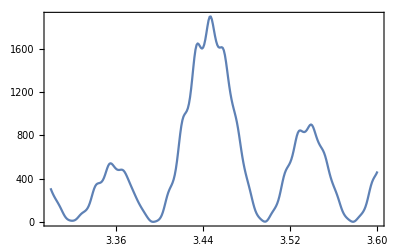

```mathematica
ListLinePlot[tk08s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk08sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/2,0]},{x,3.3,3.6,0.001}]
```

(3.3 | 10.3009
3.301 | 15.5386
3.302 | 25.0877
3.303 | 37.3961
3.304 | 51.5568
3.305 | 67.5502
3.306 | 86.2124
3.307 | 109.08
3.308 | 138.128
3.309 | 175.299
3.31 | 221.7
3.311 | 276.604
3.312 | 336.862
3.313 | 397.557
3.314 | 453.976
3.315 | 503.65
3.316 | 547.098
3.317 | 587.169
3.318 | 627.907
3.319 | 673.635
3.32 | 728.372
3.321 | 795.278
3.322 | 875.819
3.323 | 968.528
3.324 | 1067.87
3.325 | 1164.45
3.326 | 1247.68
3.327 | 1310.25
3.328 | 1351.33
3.329 | 1376.3
3.33 | 1393.78
3.331 | 1412.63
3.332 | 1440.14
3.333 | 1481.46
3.334 | 1539.26
3.335 | 1613.16
3.336 | 1698.65
3.337 | 1786.33
3.338 | 1862.84
3.339 | 1914.77
3.34 | 1934.4
3.341 | 1923.4
3.342 | 1891.49
3.343 | 1851.58
3.344 | 1815.25
3.345 | 1790.57
3.346 | 1781.84
3.347 | 1789.94
3.348 | 1812.39
3.349 | 1843.03
3.35 | 1871.89
3.351 | 1886.49
3.352 | 1875.46
3.353 | 1833.56
3.354 | 1764.52
3.355 | 1679.2
3.356 | 1590.37
3.357 | 1508.23
3.358 | 1438.66
3.359 | 1383.49
3.36 | 1341.44
3.361 | 1308.87
3.362 | 1280.14
3.363 | 1248.07
3.364 | 1205.1
3.365 | 1145.67
3.366 | 1068.89
3.367 | 979.513
3.368 | 885.884
3.369 | 796.162
3.37 | 715.609
3.371 | 646.008
3.372 | 586.493
3.373 | 534.669
3.374 | 487.449
3.375 | 441.62
3.376 | 394.359
3.377 | 343.91
3.378 | 290.344
3.379 | 235.893
3.38 | 184.239
3.381 | 138.889
3.382 | 101.729
3.383 | 72.7113
3.384 | 50.5281
3.385 | 33.5301
3.386 | 20.3978
3.387 | 10.4993
3.388 | 4.04115
3.389 | 2.06652
3.39 | 6.22221
3.391 | 18.1555
3.392 | 38.5933
3.393 | 66.6108
3.394 | 99.7988
3.395 | 135.402
3.396 | 171.613
3.397 | 208.211
3.398 | 246.503
3.399 | 288.943
3.4 | 338.725
3.401 | 399.323
3.402 | 473.757
3.403 | 563.357
3.404 | 666.184
3.405 | 776.02
3.406 | 883.47
3.407 | 979.59
3.408 | 1059.96
3.409 | 1126.25
3.41 | 1184.79
3.411 | 1243.9
3.412 | 1311.91
3.413 | 1396.14
3.414 | 1502.16
3.415 | 1632.73
3.416 | 1786.01
3.417 | 1953.42
3.418 | 2119.17
3.419 | 2263.75
3.42 | 2371.71
3.421 | 2438.96
3.422 | 2474.07
3.423 | 2493.32
3.424 | 2514.22
3.425 | 2551.43
3.426 | 2615.39
3.427 | 2712.05
3.428 | 2842.25
3.429 | 3000.06
3.43 | 3170.82
3.431 | 3331.09
3.432 | 3453.76
3.433 | 3518.58
3.434 | 3522.17
3.435 | 3479.42
3.436 | 3415.54
3.437 | 3355.8
3.438 | 3319.38
3.439 | 3317.88
3.44 | 3356.03
3.441 | 3432.07
3.442 | 3537.01
3.443 | 3653.33
3.444 | 3755.3
3.445 | 3814.06
3.446 | 3808.36
3.447 | 3735.28
3.448 | 3612.22
3.449 | 3468.02
3.45 | 3330.85
3.451 | 3220.75
3.452 | 3148.27
3.453 | 3115.94
3.454 | 3119.84
3.455 | 3150.03
3.456 | 3190.1
3.457 | 3217.67
3.458 | 3208.43
3.459 | 3144.54
3.46 | 3023.69
3.461 | 2861.36
3.462 | 2683.32
3.463 | 2514.51
3.464 | 2371.82
3.465 | 2262.93
3.466 | 2188.17
3.467 | 2142.74
3.468 | 2117.89
3.469 | 2101.15
3.47 | 2076.99
3.471 | 2029.27
3.472 | 1946.39
3.473 | 1827.1
3.474 | 1682.24
3.475 | 1529.85
3.476 | 1387.13
3.477 | 1265.19
3.478 | 1168.16
3.479 | 1094.96
3.48 | 1041.34
3.481 | 1001.14
3.482 | 966.86
3.483 | 930.172
3.484 | 883.069
3.485 | 820.19
3.486 | 741.421
3.487 | 652.623
3.488 | 563.106
3.489 | 481.463
3.49 | 412.751
3.491 | 358.191
3.492 | 316.356
3.493 | 284.49
3.494 | 259.376
3.495 | 237.759
3.496 | 216.605
3.497 | 193.464
3.498 | 167.053
3.499 | 137.82
3.5 | 107.89
3.501 | 80.1131
3.502 | 56.7428
3.503 | 38.7017
3.504 | 25.6959
3.505 | 16.7659
3.506 | 10.7982
3.507 | 6.82789
3.508 | 4.17069
3.509 | 2.46806
3.51 | 1.68663
3.511 | 2.05507
3.512 | 3.89761
3.513 | 7.38495
3.514 | 12.346
3.515 | 18.2934
3.516 | 24.635
3.517 | 30.8907
3.518 | 36.7901
3.519 | 42.2642
3.52 | 47.3954
3.521 | 52.3686
3.522 | 57.4296
3.523 | 62.8319
3.524 | 68.7539
3.525 | 75.1921
3.526 | 81.894
3.527 | 88.4159
3.528 | 94.3041
3.529 | 99.2687
3.53 | 103.233
3.531 | 106.264
3.532 | 108.475
3.533 | 109.947
3.534 | 110.689
3.535 | 110.631
3.536 | 109.646
3.537 | 107.61
3.538 | 104.504
3.539 | 100.513
3.54 | 96.0277
3.541 | 91.5069
3.542 | 87.2855
3.543 | 83.4627
3.544 | 79.9212
3.545 | 76.4102
3.546 | 72.6228
3.547 | 68.2481
3.548 | 63.0151
3.549 | 56.7559
3.55 | 49.5044
3.551 | 41.5999
3.552 | 33.7043
3.553 | 26.6248
3.554 | 20.9784
3.555 | 16.9293
3.556 | 14.1969
3.557 | 12.2773
3.558 | 10.6813
3.559 | 9.0757
3.56 | 7.338
3.561 | 5.57535
3.562 | 4.13388
3.563 | 3.5808
3.564 | 4.60029
3.565 | 7.75064
3.566 | 13.1425
3.567 | 20.2678
3.568 | 28.188
3.569 | 35.978
3.57 | 43.0959
3.571 | 49.4935
3.572 | 55.5421
3.573 | 61.9164
3.574 | 69.5046
3.575 | 79.3168
3.576 | 92.3143
3.577 | 109.08
3.578 | 129.362
3.579 | 151.768
3.58 | 174.027
3.581 | 193.905
3.582 | 210.167
3.583 | 222.912
3.584 | 233.24
3.585 | 242.711
3.586 | 252.966
3.587 | 265.521
3.588 | 281.643
3.589 | 302.12
3.59 | 326.887
3.591 | 354.573
3.592 | 382.394
3.593 | 406.871
3.594 | 425.271
3.595 | 436.821
3.596 | 442.775
3.597 | 445.524
3.598 | 447.605
3.599 | 451.128
3.6 | 457.593)

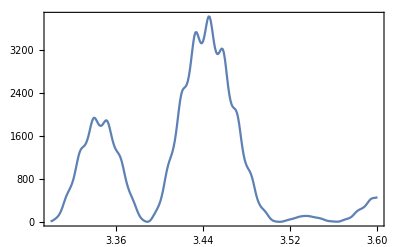

```mathematica
ListLinePlot[tk08sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/4,0]},{x,2.5,3.5,0.005}]
```

(2.5 | 3274.95
2.505 | 3898.71
2.51 | 4620.45
2.515 | 4374.06
2.52 | 4388.41
2.525 | 3440.2
2.53 | 2721.55
2.535 | 1751.12
2.54 | 818.065
2.545 | 318.39
2.55 | 0.317075
2.555 | 114.78
2.56 | 679.048
2.565 | 1442.13
2.57 | 2267.27
2.575 | 3394.61
2.58 | 3816.27
2.585 | 4560.84
2.59 | 4306.66
2.595 | 4133.57
2.6 | 3420.5
2.605 | 2457.86
2.61 | 1716.59
2.615 | 699.59
2.62 | 260.494
2.625 | 0.926494
2.63 | 173.038
2.635 | 657.421
2.64 | 1579.
2.645 | 2259.07
2.65 | 3425.56
2.655 | 3836.1
2.66 | 4377.82
2.665 | 4329.44
2.67 | 3862.37
2.675 | 3400.57
2.68 | 2258.04
2.685 | 1593.48
2.69 | 644.506
2.695 | 187.539
2.7 | 0.684562
2.705 | 239.02
2.71 | 671.699
2.715 | 1660.24
2.72 | 2338.66
2.725 | 3340.17
2.73 | 3930.01
2.735 | 4168.81
2.74 | 4359.89
2.745 | 3658.07
2.75 | 3271.39
2.755 | 2151.55
2.76 | 1405.42
2.765 | 632.848
2.77 | 122.823
2.775 | 0.457692
2.78 | 290.925
2.785 | 743.686
2.79 | 1655.34
2.795 | 2476.31
2.8 | 3218.41
2.805 | 4029.36
2.81 | 4024.81
2.815 | 4281.98
2.82 | 3553.16
2.825 | 3032.98
2.83 | 2121.77
2.835 | 1213.28
2.84 | 609.383
2.845 | 79.1481
2.85 | 8.03646
2.855 | 310.367
2.86 | 855.536
2.865 | 1608.77
2.87 | 2616.74
2.875 | 3151.69
2.88 | 4030.86
2.885 | 3971.09
2.89 | 4064.01
2.895 | 3528.38
2.9 | 2765.47
2.905 | 2085.02
2.91 | 1059.61
2.915 | 536.908
2.92 | 59.2558
2.925 | 27.0661
2.93 | 305.179
2.935 | 969.481
2.94 | 1590.34
2.945 | 2668.02
2.95 | 3140.81
2.955 | 3849.17
2.96 | 3936.49
2.965 | 3733.35
2.97 | 3426.33
2.975 | 2466.12
2.98 | 1875.19
2.985 | 900.539
2.99 | 383.463
2.995 | 34.6676
3. | 77.5296
3.005 | 379.599
3.01 | 1178.94
3.015 | 1804.88
3.02 | 2848.43
3.025 | 3455.41
3.03 | 3916.21
3.035 | 4249.55
3.04 | 3764.41
3.045 | 3564.54
3.05 | 2521.84
3.055 | 1836.31
3.06 | 976.808
3.065 | 341.968
3.07 | 49.8121
3.075 | 83.9336
3.08 | 381.434
3.085 | 1129.45
3.09 | 1846.49
3.095 | 2662.04
3.1 | 3489.49
3.105 | 3698.81
3.11 | 4151.21
3.115 | 3604.34
3.12 | 3298.74
3.125 | 2453.47
3.13 | 1603.25
3.135 | 940.112
3.14 | 259.126
3.145 | 35.9446
3.15 | 100.766
3.155 | 463.854
3.16 | 1110.11
3.165 | 1982.52
3.17 | 2601.01
3.175 | 3538.5
3.18 | 3642.81
3.185 | 3975.38
3.19 | 3575.44
3.195 | 3024.69
3.2 | 2419.98
3.205 | 1417.36
3.21 | 855.24
3.215 | 210.948
3.22 | 20.5221
3.225 | 106.457
3.23 | 561.661
3.235 | 1113.91
3.24 | 2088.46
3.245 | 2625.57
3.25 | 3474.44
3.255 | 3676.65
3.26 | 3740.69
3.265 | 3582.64
3.27 | 2793.27
3.275 | 2311.25
3.28 | 1296.8
3.285 | 722.533
3.29 | 191.049
3.295 | 10.9677
3.3 | 117.688
3.305 | 647.872
3.31 | 1174.97
3.315 | 2112.91
3.32 | 2719.82
3.325 | 3335.72
3.33 | 3746.53
3.335 | 3538.68
3.34 | 3515.59
3.345 | 2640.08
3.35 | 2104.7
3.355 | 1238.4
3.36 | 579.425
3.365 | 174.021
3.37 | 9.58439
3.375 | 152.244
3.38 | 697.005
3.385 | 1286.83
3.39 | 2073.19
3.395 | 2844.85
3.4 | 3218.29
3.405 | 3761.78
3.41 | 3415.73
3.415 | 3319.96
3.42 | 2567.01
3.425 | 1860.41
3.43 | 1194.65
3.435 | 457.538
3.44 | 139.104
3.445 | 13.5902
3.45 | 212.342
3.455 | 710.131
3.46 | 1423.
3.465 | 2045.39
3.47 | 2937.14
3.475 | 3173.93
3.48 | 3652.24
3.485 | 3374.75
3.49 | 3055.85
3.495 | 2526.51
3.5 | 1640.24)

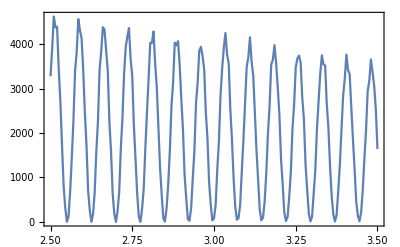

```mathematica
ListLinePlot[tk07s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/4,0]},{x,2.5,3.5,0.005}]
```

(2.5 | 437.064
2.505 | 92.0254
2.51 | 68.0974
2.515 | 457.88
2.52 | 1199.14
2.525 | 2264.58
2.53 | 3068.61
2.535 | 4335.92
2.54 | 4574.67
2.545 | 5151.09
2.55 | 4852.02
2.555 | 4230.71
2.56 | 3644.21
2.565 | 2330.86
2.57 | 1586.27
2.575 | 602.313
2.58 | 154.939
2.585 | 9.11366
2.59 | 335.672
2.595 | 873.433
2.6 | 1973.08
2.605 | 2707.47
2.61 | 3881.84
2.615 | 4437.39
2.62 | 4748.96
2.625 | 4979.49
2.63 | 4174.09
2.635 | 3807.63
2.64 | 2567.13
2.645 | 1724.5
2.65 | 847.166
2.655 | 221.013
2.66 | 9.56967
2.665 | 212.035
2.67 | 652.593
2.675 | 1592.91
2.68 | 2453.93
2.685 | 3351.17
2.69 | 4317.65
2.695 | 4430.61
2.7 | 4931.95
2.705 | 4250.02
2.71 | 3806.05
2.715 | 2903.16
2.72 | 1844.53
2.725 | 1117.06
2.73 | 316.821
2.735 | 48.5654
2.74 | 93.5496
2.745 | 500.491
2.75 | 1194.11
2.755 | 2226.85
2.76 | 2912.24
2.765 | 4069.71
2.77 | 4262.17
2.775 | 4682.19
2.78 | 4439.78
2.785 | 3771.93
2.79 | 3236.64
2.795 | 2023.39
2.8 | 1337.49
2.805 | 482.493
2.81 | 99.7564
2.815 | 16.676
2.82 | 370.618
2.825 | 881.753
2.83 | 1941.42
2.835 | 2620.7
2.84 | 3659.68
2.845 | 4218.74
2.85 | 4404.11
2.855 | 4638.1
2.86 | 3839.44
2.865 | 3456.08
2.87 | 2327.6
2.875 | 1512.86
2.88 | 736.894
2.885 | 164.176
2.89 | 2.65309
2.895 | 237.083
2.9 | 680.207
2.905 | 1584.42
2.91 | 2453.43
2.915 | 3258.37
2.92 | 4242.56
2.925 | 4303.74
2.93 | 4768.45
2.935 | 4139.3
2.94 | 3644.95
2.945 | 2823.95
2.95 | 1749.29
2.955 | 1061.8
2.96 | 282.82
2.965 | 32.8802
2.97 | 111.528
2.975 | 567.978
2.98 | 1305.76
2.985 | 2478.75
2.99 | 3241.52
2.995 | 4621.27
3. | 4960.46
3.005 | 5559.65
3.01 | 5597.27
3.015 | 4903.73
3.02 | 4646.75
3.025 | 3233.18
3.03 | 2504.
3.035 | 1426.21
3.04 | 629.05
3.045 | 206.55
3.05 | 2.56704
3.055 | 123.027
3.06 | 574.445
3.065 | 1084.11
3.07 | 1666.71
3.075 | 2221.49
3.08 | 2458.82
3.085 | 2693.03
3.09 | 2358.22
3.095 | 2159.64
3.1 | 1487.36
3.105 | 989.131
3.11 | 491.966
3.115 | 101.324
3.12 | 1.65964
3.125 | 171.363
3.13 | 488.402
3.135 | 1093.93
3.14 | 1778.39
3.145 | 2296.06
3.15 | 3029.71
3.155 | 3099.99
3.16 | 3376.74
3.165 | 2980.92
3.17 | 2601.77
3.175 | 2019.09
3.18 | 1243.39
3.185 | 764.991
3.19 | 195.844
3.195 | 24.0143
3.2 | 71.998
3.205 | 401.876
3.21 | 856.376
3.215 | 1676.36
3.22 | 2143.35
3.225 | 2937.27
3.23 | 3167.16
3.235 | 3357.82
3.24 | 3270.99
3.245 | 2730.72
3.25 | 2357.16
3.255 | 1463.39
3.26 | 961.27
3.265 | 355.731
3.27 | 60.9719
3.275 | 9.39159
3.28 | 288.908
3.285 | 646.418
3.29 | 1417.54
3.295 | 1977.57
3.3 | 2632.35
3.305 | 3167.66
3.31 | 3230.3
3.315 | 3424.69
3.32 | 2854.61
3.325 | 2536.92
3.33 | 1748.23
3.335 | 1109.09
3.34 | 576.291
3.345 | 115.817
3.35 | 3.08436
3.355 | 162.545
3.36 | 498.3
3.365 | 1087.75
3.37 | 1814.62
3.375 | 2312.9
3.38 | 3068.58
3.385 | 3135.18
3.39 | 3396.41
3.395 | 3032.
3.4 | 2611.27
3.405 | 2075.26
3.41 | 1260.29
3.415 | 793.816
3.42 | 215.097
3.425 | 28.4703
3.43 | 54.847
3.435 | 378.018
3.44 | 797.32
3.445 | 1601.84
3.45 | 2066.79
3.455 | 2818.24
3.46 | 3092.86
3.465 | 3249.72
3.47 | 3224.56
3.475 | 2673.73
3.48 | 2338.2
3.485 | 1467.75
3.49 | 962.304
3.495 | 385.136
3.5 | 67.3862)

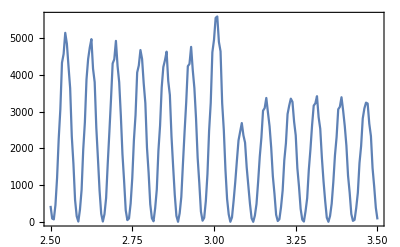

```mathematica
ListLinePlot[tk07sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
ll2ts1=AmplTwistTab[1,3.45/mee,3.45/mee/2];
ll2tsm1=AmplTwistTab[-1,3.45/mee,3.45/mee/2];
```

```mathematica
tm2s1=Table[{m,dProbabTwist[m,ll2ts1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,ll2tsm1[[3]]]},{m,-mMax,mMax}];
```

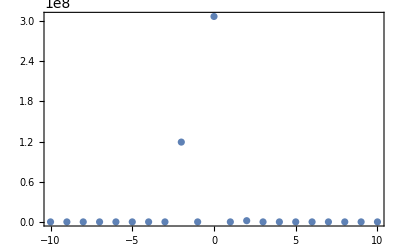
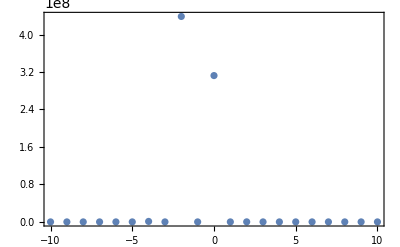

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ll3ts1=AmplTwistTab[1,3.47/mee,3.47/mee/2];(*смещение на 0.02 эВ оказывается существенным для распределения по m*)
ll3tsm1=AmplTwistTab[-1,3.47/mee,3.47/mee/2];
```

```mathematica
tm3s1=Table[{m,dProbabTwist[m,ll3ts1[[3]]]},{m,-mMax,mMax}];
tm3sm1=Table[{m,dProbabTwist[m,ll3tsm1[[3]]]},{m,-mMax,mMax}];
```

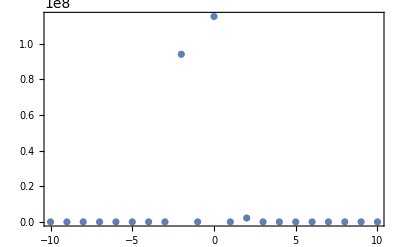
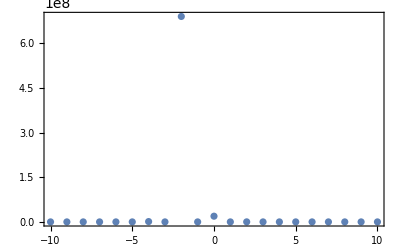

```mathematica
{ListPlot[tm3s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm3sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
llts1=AmplTwistTab[1,3.47/mee,3.47/mee/2];
lltsm1=AmplTwistTab[-1,3.47/mee,3.47/mee/2];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

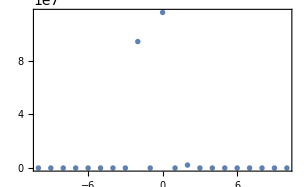
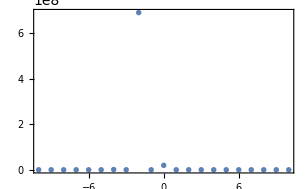

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*---------------------------------старое----------------------------------------------------------------------*)
```

```mathematica
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,2,6,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.564×10^7}. NIntegrate obtained -103.024+749.105 ⅈ and 0.00567985 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained 4327.8-15795.2 ⅈ and 0.0176848 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.18131×10^7}. NIntegrate obtained 29.3679-145.303 ⅈ and 0.00919226 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.14908×10^7}. NIntegrate obtained -1787.86-6979.94 ⅈ and 0.0194582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.70194×10^7}. NIntegrate obtained -8401.67+537.989 ⅈ and 0.0232889 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.52165×10^7}. NIntegrate obtained -1709.83-11757.2 ⅈ and 0.0123737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.48942×10^7}. NIntegrate obtained -2407.62-2149.24 ⅈ and 0.0146859 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(2. | 2388.
2.05 | 7345.89
2.1 | 5612.29
2.15 | 1733.5
2.2 | 8441.13
2.25 | 34.5879
2.3 | 6968.52
2.35 | 2522.95
2.4 | 4003.12
2.45 | 6702.27
2.5 | 888.128
2.55 | 9296.11
2.6 | 439.022
2.65 | 7675.53
2.7 | 2599.2
2.75 | 2906.12
2.8 | 5755.46
2.85 | 140.931
2.9 | 6158.78
2.95 | 1666.69
3. | 4466.85
3.05 | 5142.65
3.1 | 1223.06
3.15 | 7732.3
3.2 | 224.736
3.25 | 4861.09
3.3 | 2506.28
3.35 | 1543.33
3.4 | 5569.63
3.45 | 195.913
3.5 | 6227.43
3.55 | 2275.52
3.6 | 3226.04
3.65 | 4838.82
3.7 | 167.769
3.75 | 4747.18
3.8 | 1262.42
3.85 | 2410.13
3.9 | 5282.52
3.95 | 421.15
4. | 6039.98
4.05 | 792.638
4.1 | 3302.84
4.15 | 3077.32
4.2 | 120.563
4.25 | 5180.97
4.3 | 1208.1
4.35 | 3364.82
4.4 | 4004.49
4.45 | 540.477
4.5 | 4008.82
4.55 | 907.939
4.6 | 2097.72
4.65 | 4105.44
4.7 | 336.22
4.75 | 5345.79
4.8 | 877.355
4.85 | 2067.89
4.9 | 3131.46
4.95 | 51.3741
5. | 4307.54
5.05 | 1811.58
5.1 | 2126.64
5.15 | 3694.26
5.2 | 26.8753
5.25 | 3002.47
5.3 | 1986.89
5.35 | 966.151
5.4 | 4675.27
5.45 | 203.975
5.5 | 3424.09
5.55 | 1674.09
5.6 | 348.364
5.65 | 4041.35
5.7 | 725.738
5.75 | 2883.85
5.8 | 2705.18
5.85 | 318.426
5.9 | 2885.82
5.95 | 1262.43
6. | 1416.36)

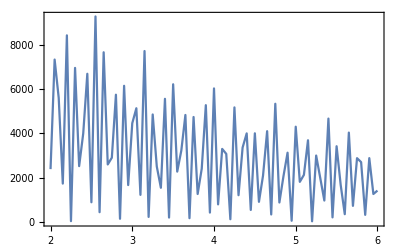

```mathematica
ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,2,6,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6.27354×10^6}. NIntegrate obtained -876.223-8206.83 ⅈ and 0.0112262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.04227×10^7}. NIntegrate obtained 411.301+4976.65 ⅈ and 0.00924172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.8721×10^7}. NIntegrate obtained 5869.61-4910.76 ⅈ and 0.0123659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.12438×10^6}. NIntegrate obtained 1719.01-13708.5 ⅈ and 0.0281095 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.73417×10^7}. NIntegrate obtained -3648.92-448.239 ⅈ and 0.0149327 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {8.29752×10^6}. NIntegrate obtained -482.112-7548.33 ⅈ and 0.0306348 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.90433×10^7}. NIntegrate obtained 9931.08+9339.77 ⅈ and 0.03338 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

(2. | 6209.34
2.05 | 267.484
2.1 | 7188.76
2.15 | 181.001
2.2 | 8556.39
2.25 | 147.35
2.3 | 7957.96
2.35 | 472.654
2.4 | 8338.7
2.45 | 36.8336
2.5 | 3338.87
2.55 | 305.195
2.6 | 3743.49
2.65 | 317.568
2.7 | 4721.26
2.75 | 286.331
2.8 | 5997.45
2.85 | 263.476
2.9 | 5418.48
2.95 | 34.6184
3. | 3909.7
3.05 | 511.407
3.1 | 2528.42
3.15 | 1727.03
3.2 | 2114.36
3.25 | 2086.89
3.3 | 3146.84
3.35 | 2303.66
3.4 | 2961.67
3.45 | 1244.27
3.5 | 1358.92
3.55 | 1796.18
3.6 | 508.116
3.65 | 3819.52
3.7 | 168.578
3.75 | 4579.48
3.8 | 266.093
3.85 | 3361.23
3.9 | 485.982
3.95 | 1665.71
4. | 626.273
4.05 | 2303.34
4.1 | 1213.77
4.15 | 3222.
4.2 | 604.9
4.25 | 2918.43
4.3 | 687.228
4.35 | 1096.31
4.4 | 1944.27
4.45 | 141.09
4.5 | 3324.47
4.55 | 591.505
4.6 | 2832.24
4.65 | 487.206
4.7 | 1213.45
4.75 | 857.116
4.8 | 1933.29
4.85 | 761.713
4.9 | 3003.5
4.95 | 477.492
5. | 2298.75
5.05 | 686.098
5.1 | 316.965
5.15 | 2223.67
5.2 | 123.825
5.25 | 3091.1
5.3 | 492.177
5.35 | 1427.58
5.4 | 642.905
5.45 | 1046.43
5.5 | 1158.34
5.55 | 2051.02
5.6 | 711.669
5.65 | 2227.32
5.7 | 495.907
5.75 | 481.412
5.8 | 1807.55
5.85 | 0.59991
5.9 | 2889.6
5.95 | 243.087
6. | 1335.89)

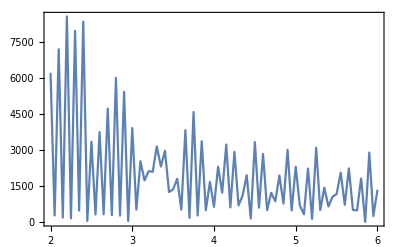

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,2,3,0.01}]
```

(2. | 2388.
2.01 | 5779.29
2.02 | 9012.97
2.03 | 11370.8
2.04 | 9251.5
2.05 | 7345.89
2.06 | 2899.37
2.07 | 591.704
2.08 | 416.831
2.09 | 2598.48
2.1 | 5612.29
2.11 | 8896.78
2.12 | 9691.71
2.13 | 7974.55
2.14 | 5673.97
2.15 | 1733.5
2.16 | 265.19
2.17 | 680.307
2.18 | 2808.11
2.19 | 5761.84
2.2 | 8441.13
2.21 | 7966.41
2.22 | 6604.99
2.23 | 3592.61
2.24 | 792.85
2.25 | 34.5879
2.26 | 1409.65
2.27 | 3474.2
2.28 | 6614.17
2.29 | 7983.7
2.3 | 6968.52
2.31 | 5268.85
2.32 | 2053.2
2.33 | 249.513
2.34 | 293.611
2.35 | 2522.95
2.36 | 4673.64
2.37 | 7916.44
2.38 | 7744.09
2.39 | 6591.27
2.4 | 4003.12
2.41 | 1168.97
2.42 | 97.9358
2.43 | 1226.27
2.44 | 3905.61
2.45 | 6702.27
2.46 | 9472.6
2.47 | 8443.54
2.48 | 6966.84
2.49 | 3491.03
2.5 | 888.128
2.51 | 196.213
2.52 | 1859.17
2.53 | 4472.19
2.54 | 7799.5
2.55 | 9296.11
2.56 | 8320.25
2.57 | 6293.83
2.58 | 2689.73
2.59 | 658.61
2.6 | 439.022
2.61 | 2348.17
2.62 | 5057.78
2.63 | 8214.62
2.64 | 8490.32
2.65 | 7675.53
2.66 | 4870.93
2.67 | 1777.2
2.68 | 320.657
2.69 | 650.725
2.7 | 2599.2
2.71 | 5304.62
2.72 | 7601.12
2.73 | 7008.45
2.74 | 6185.86
2.75 | 2906.12
2.76 | 839.688
2.77 | 74.3552
2.78 | 1184.86
2.79 | 3143.35
2.8 | 5755.46
2.81 | 6594.15
2.82 | 5645.82
2.83 | 4127.51
2.84 | 1281.92
2.85 | 140.931
2.86 | 482.074
2.87 | 2336.04
2.88 | 4429.74
2.89 | 6711.67
2.9 | 6158.78
2.91 | 4895.03
2.92 | 2564.45
2.93 | 461.077
2.94 | 82.9961
2.95 | 1666.69
2.96 | 3803.24
2.97 | 6350.41
2.98 | 7545.93
2.99 | 6398.47
3. | 4466.85)

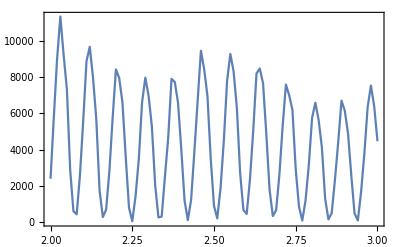

```mathematica
ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,2,3,0.01}]
```

(2. | 6209.34
2.01 | 5604.66
2.02 | 2998.75
2.03 | 1847.44
2.04 | 171.101
2.05 | 267.484
2.06 | 1313.38
2.07 | 3463.32
2.08 | 5254.99
2.09 | 7152.31
2.1 | 7188.76
2.11 | 5989.29
2.12 | 4440.08
2.13 | 1579.81
2.14 | 484.04
2.15 | 181.001
2.16 | 1184.96
2.17 | 3814.71
2.18 | 6305.39
2.19 | 7658.5
2.2 | 8556.39
2.21 | 6586.99
2.22 | 4396.91
2.23 | 1968.95
2.24 | 150.997
2.25 | 147.35
2.26 | 2106.05
2.27 | 4074.08
2.28 | 7088.33
2.29 | 8567.88
2.3 | 7957.96
2.31 | 6986.61
2.32 | 3712.13
2.33 | 1527.34
2.34 | 138.306
2.35 | 472.654
2.36 | 1903.86
2.37 | 5207.49
2.38 | 6697.46
2.39 | 8654.24
2.4 | 8338.7
2.41 | 6421.34
2.42 | 4825.83
2.43 | 1848.76
2.44 | 774.036
2.45 | 36.8336
2.46 | 654.13
2.47 | 1605.74
2.48 | 2862.81
2.49 | 3363.6
2.5 | 3338.87
2.51 | 2939.85
2.52 | 1619.48
2.53 | 1158.76
2.54 | 259.8
2.55 | 305.195
2.56 | 837.181
2.57 | 1349.3
2.58 | 2600.54
2.59 | 3125.63
2.6 | 3743.49
2.61 | 3590.81
2.62 | 3043.15
2.63 | 2023.46
2.64 | 1059.12
2.65 | 317.568
2.66 | 88.2399
2.67 | 1027.7
2.68 | 1857.14
2.69 | 3694.34
2.7 | 4721.26
2.71 | 4914.42
2.72 | 4837.31
2.73 | 2908.47
2.74 | 1708.94
2.75 | 286.331
2.76 | 59.8569
2.77 | 834.862
2.78 | 2829.68
2.79 | 4293.41
2.8 | 5997.45
2.81 | 6150.92
2.82 | 4877.67
2.83 | 3626.04
2.84 | 1240.
2.85 | 263.476
2.86 | 187.171
2.87 | 1243.08
2.88 | 2886.12
2.89 | 5009.28
2.9 | 5418.48
2.91 | 5600.39
2.92 | 4304.47
2.93 | 2330.37
2.94 | 1117.63
2.95 | 34.6184
2.96 | 147.112
2.97 | 1247.28
2.98 | 2247.1
2.99 | 3526.07
3. | 3909.7)

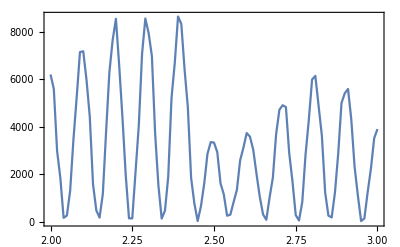

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
llts1=AmplTwistTab[1,2.46/mee,2.46/mee/5];
lltsm1=AmplTwistTab[-1,2.46/mee,2.46/mee/5];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

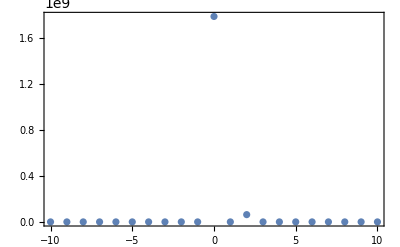
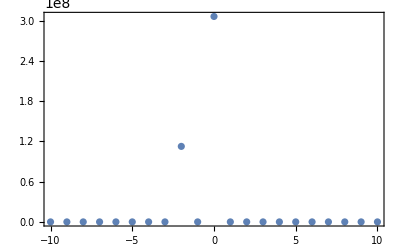

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
tk03s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/10,0]},{x,2,3,0.01}]
```

(2. | 46366.1
2.01 | 39839.5
2.02 | 32891.5
2.03 | 14545.7
2.04 | 3623.66
2.05 | 1359.5
2.06 | 9321.5
2.07 | 21954.3
2.08 | 35639.8
2.09 | 41141.6
2.1 | 33833.
2.11 | 25270.4
2.12 | 8280.64
2.13 | 1396.93
2.14 | 2506.66
2.15 | 11603.1
2.16 | 23498.4
2.17 | 34901.5
2.18 | 34018.7
2.19 | 26707.
2.2 | 15823.9
2.21 | 3145.33
2.22 | 122.804
2.23 | 5743.5
2.24 | 15047.4
2.25 | 26243.4
2.26 | 33170.1
2.27 | 27511.1
2.28 | 19509.
2.29 | 7803.62
2.3 | 383.399
2.31 | 1371.9
2.32 | 11829.9
2.33 | 20262.9
2.34 | 30861.2
2.35 | 31260.9
2.36 | 23007.9
2.37 | 13162.5
2.38 | 3058.11
2.39 | 347.993
2.4 | 5930.35
2.41 | 19762.2
2.42 | 27376.4
2.43 | 36560.7
2.44 | 30582.6
2.45 | 20730.3
2.46 | 9155.11
2.47 | 1364.72
2.48 | 2194.75
2.49 | 11756.4
2.5 | 25369.7
2.51 | 32989.4
2.52 | 38311.3
2.53 | 28330.7
2.54 | 17774.8
2.55 | 5870.39
2.56 | 1022.81
2.57 | 5040.49
2.58 | 16872.5
2.59 | 28364.2
2.6 | 35237.2
2.61 | 35371.3
2.62 | 23478.4
2.63 | 13266.
2.64 | 2688.64
2.65 | 1108.13
2.66 | 7855.73
2.67 | 19649.1
2.68 | 28064.2
2.69 | 32843.6
2.7 | 27561.
2.71 | 16071.9
2.72 | 6975.15
2.73 | 349.687
2.74 | 2204.1
2.75 | 11267.4
2.76 | 21224.4
2.77 | 25828.9
2.78 | 27314.1
2.79 | 17756.7
2.8 | 8329.23
2.81 | 1610.61
2.82 | 992.892
2.83 | 5954.4
2.84 | 17199.1
2.85 | 23219.1
2.86 | 24572.
2.87 | 20809.8
2.88 | 10112.5
2.89 | 2661.77
2.9 | 321.848
2.91 | 5531.51
2.92 | 13037.6
2.93 | 25342.8
2.94 | 26427.1
2.95 | 24856.7
2.96 | 15955.2
2.97 | 5861.86
2.98 | 688.02
2.99 | 3038.77
3. | 11677.6)

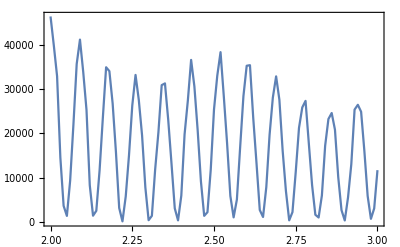

```mathematica
ListLinePlot[tk03s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk03sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/10,0]},{x,2,3,0.01}]
```

(2. | 5696.75
2.01 | 467.986
2.02 | 2088.2
2.03 | 6159.37
2.04 | 14666.1
2.05 | 20474.5
2.06 | 25888.4
2.07 | 25852.9
2.08 | 19218.8
2.09 | 14312.6
2.1 | 3862.42
2.11 | 942.043
2.12 | 1621.18
2.13 | 6823.69
2.14 | 16489.8
2.15 | 25991.2
2.16 | 29157.2
2.17 | 29518.4
2.18 | 22321.
2.19 | 11551.5
2.2 | 4714.3
2.21 | 14.4277
2.22 | 2000.31
2.23 | 11812.8
2.24 | 20754.
2.25 | 29011.5
2.26 | 33936.4
2.27 | 27363.4
2.28 | 20357.8
2.29 | 9498.35
2.3 | 1469.09
2.31 | 214.82
2.32 | 6224.84
2.33 | 12821.
2.34 | 24879.1
2.35 | 29590.4
2.36 | 29182.9
2.37 | 25543.4
2.38 | 14416.4
2.39 | 6681.81
2.4 | 894.794
2.41 | 939.911
2.42 | 4099.09
2.43 | 12987.2
2.44 | 16216.7
2.45 | 21075.1
2.46 | 19204.4
2.47 | 13997.
2.48 | 9644.11
2.49 | 2925.29
2.5 | 1609.52
2.51 | 1062.96
2.52 | 5003.27
2.53 | 8101.01
2.54 | 13105.2
2.55 | 14742.7
2.56 | 14956.9
2.57 | 14223.3
2.58 | 9015.35
2.59 | 7480.79
2.6 | 2146.05
2.61 | 1643.55
2.62 | 1960.83
2.63 | 4253.11
2.64 | 9739.97
2.65 | 13858.
2.66 | 17603.8
2.67 | 17944.9
2.68 | 15620.6
2.69 | 9439.15
2.7 | 5028.29
2.71 | 433.394
2.72 | 311.743
2.73 | 5578.6
2.74 | 11013.
2.75 | 18983.1
2.76 | 24042.2
2.77 | 22191.9
2.78 | 19217.1
2.79 | 10572.7
2.8 | 3460.89
2.81 | 327.513
2.82 | 2209.37
2.83 | 6843.17
2.84 | 16854.2
2.85 | 21958.1
2.86 | 24433.5
2.87 | 23091.8
2.88 | 14540.9
2.89 | 7885.42
2.9 | 1696.23
2.91 | 184.309
2.92 | 2610.01
2.93 | 10384.2
2.94 | 14007.7
2.95 | 20071.
2.96 | 18710.9
2.97 | 15041.
2.98 | 10395.9
2.99 | 3897.87
3. | 1696.85)

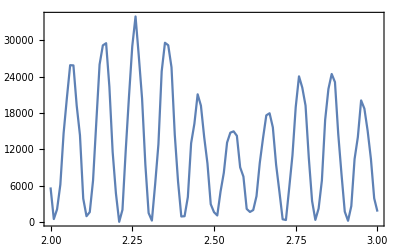

```mathematica
ListLinePlot[tk03sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
(*старое*)
```